# dirac16complex dark sector: symbolic reduction and NDSolve cross-check of the Rust CVODE study

This notebook is generated by scripts/build_dirac16complex_mathematica_notebook.wls and verified headless by scripts/verify_dirac16complex_mathematica_notebook.wls. It checks the Stage-3 numerics of the 16-component complex Grassmann spinor field dirac16complex (Rust crate studies/dirac16complex_cosmology, integrated with the pure-Rust SUNDIALS 7.8.0 CVODE engine of rustSolveIt) in three independent ways: (1) for every experiment the reduced first-order ODE system is derived symbolically from the covariant field equations of CONTRACT.md in the experiment's background and compared exactly with the mode Hamiltonian the Rust code implements; the Clifford matrices compiled into the binary (src/generated.rs) are read back and compared entry by entry; the Rust solution files are differentiated with 9-point finite differences and compared with the derived right-hand side; (2) every experiment is re-integrated independently with NDSolve (smaller momentum grids for EXP-4) and compared with the committed CSV columns; (3) the binary is run with print-config and must end with SUCCESS.

Provenance. None of the three rustSolveIt repositories (Win11 commit a8fdff45, macOS 5360157f, Linux 6f58e02e) contains a Mathematica notebook (.nb, .wl or .wls); this was verified by listing their full git trees, and each of them has 294 Jupyter notebooks. This Mathematica notebook is therefore new. It is modelled on dirac-main's notebooks/DiracTriality.nb and its builder/verifier scripts (scripts/build_mathematica_notebook.wls, scripts/verify_mathematica_notebook.wls), including the RunProcess + Import[CSV/RawJSON] exchange with a compiled binary.

Honesty rules. Every number shown or written to artifacts/dirac16complex/numerics/mathematica-report.json is computed in this notebook from the committed outputs under artifacts/dirac16complex/numerics/exp1..exp5/ (CSV and summary.json) or from the notebook's own NDSolve and NIntegrate runs; nothing is typed in by hand. The run parameters quoted in the prose (for orientation) are compared with summary.json by a check near the end. The notebook establishes algebraic and numerical consistency between the derivation, the Rust integration and an independent integrator. It does not establish that dirac16complex is dark matter or dark energy: the backgrounds, the a4 profile of EXP-1, the 4D-effective Friedmann equation of EXP-3, the density parameters, the thermal and vacuum initial states of EXP-4 and the expectation-value rule of the mean field are modelling inputs, stated where they are used.

## Repository, packages and committed outputs

The repository root comes from $Dirac16RepositoryRoot (set by the verifier) or from the notebook's location. The two Stage-1 packages supply the gamma matrices (notebook split-octonion basis, counted from 0, eta = diag(1,1,1,1,-1,-1,-1,-1), x4 = time) and the symbolic curved-space geometry (vielbein, Levi-Civita connection, canonical spin connection Omega_mu = (1/2) omega_{mu ab} S^{ab}, Dirac operator gamma^mu D_mu).

```mathematica
repositoryRoot=If[ValueQ[$Dirac16RepositoryRoot],$Dirac16RepositoryRoot,ParentDirectory[NotebookDirectory[]]];numericsRoot=FileNameJoin[{repositoryRoot,"artifacts","dirac16complex","numerics"}];figureDirectory=FileNameJoin[{numericsRoot,"figures","mathematica"}];reportPath=FileNameJoin[{numericsRoot,"mathematica-report.json"}];Get[FileNameJoin[{repositoryRoot,"wolfram","Dirac16ComplexAlgebra.wl"}]];Get[FileNameJoin[{repositoryRoot,"wolfram","Dirac16ComplexGeometry.wl"}]];If[!DirectoryQ[figureDirectory],CreateDirectory[figureDirectory,CreateIntermediateDirectories->True]];experiments={"exp1","exp2","exp3","exp4","exp5"};summaries=AssociationMap[Import[FileNameJoin[{numericsRoot,#1,"summary.json"}],"RawJSON"]&,experiments];AssociationMap[summaries[#1]["verdict"]&,experiments]
```

## Clifford data: package, fixture and the constants compiled into the binary

gamma^a = T16^A[a] = [[0, taubar[a]], [tau[a], 0]], C = sigma16 = gamma^0 gamma^1 gamma^2 gamma^3, Psibar = Psi^dagger C, B = -i C gamma^4. The mode Hamiltonian of NUMERICS_CONTRACT is h = -i M_eff gamma^4 - gamma^4 Sum_{j != 4} (k_j/h_j) gamma^j. The expectation-value rule of the positive-norm (J = B) quantization, <Psi^dagger M Psi> = u^dagger B M u, turns the scalar density Psibar Psi into s(u) = u^dagger B C u = u^dagger (-i gamma^4) u and the time-derivative kinetic term Psibar gamma^4 D_4 Psi into u^dagger (B C gamma^4) i du/dt = u^dagger h u; the identities B C = -i gamma^4 and B C gamma^4 = i are checked exactly here.

```mathematica
gammas=Dirac16Complex`Algebra`D16Gammas;gam[a_Integer]:=gammas⟦a+1⟧;chargeC=Dirac16Complex`Algebra`D16C;kreinB=Dirac16Complex`Algebra`D16B;etaT=Dirac16Complex`Algebra`D16Eta;id16=IdentityMatrix[16];zero16=ConstantArray[0,{16,16}];transverse={0,1,2,3,5,6,7};modeHamiltonian[meff_,kh_List]:=-ⅈ meff gam[4]-∑_j^transverse kh⟦j+1⟧ gam[4].gam[j];algebraIdentities=Module[{mS,k0S,k1S,k2S,k3S,q5S,q6S,q7S,hGood,hAll},hGood=modeHamiltonian[mS,{k0S,k1S,k2S,k3S,0,0,0,0}];hAll=modeHamiltonian[mS,{k0S,k1S,k2S,k3S,0,q5S,q6S,q7S}];Association["cliffordRelations"->AllTrue[Tuples[Range[0,7],2],gam[#1⟦1⟧].gam[#1⟦2⟧]+gam[#1⟦2⟧].gam[#1⟦1⟧]==2 etaT⟦#1⟦1⟧+1,#1⟦2⟧+1⟧ id16&],"geometryPackageUsesSameGammas"->Dirac16Complex`Geometry`D16GeoGammas===gammas,"chargeIsGamma0123"->chargeC==gam[0].gam[1].gam[2].gam[3],"kreinIsMinusIChargeGamma4"->kreinB==-ⅈ chargeC.gam[4],"kreinHermitianInvolution"->kreinB==ConjugateTranspose[kreinB]&&kreinB.kreinB==id16,"scalarDensityOperatorBC"->kreinB.chargeC==-ⅈ gam[4],"kineticOperatorBCGamma4"->kreinB.chargeC.gam[4]==ⅈ id16,"hamiltonianSquaredIsE2"->Simplify[hAll.hAll-(mS^2+k0S^2+k1S^2+k2S^2+k3S^2-q5S^2-q6S^2-q7S^2) id16]===zero16,"hamiltonianHermitianInGoodSector"->Simplify[ConjugateTranspose[hGood]-hGood,{mS,k0S,k1S,k2S,k3S}∈Reals]===zero16,"hamiltonianKreinPseudoHermitian"->Simplify[ConjugateTranspose[hAll].kreinB-kreinB.hAll,{mS,k0S,k1S,k2S,k3S,q5S,q6S,q7S}∈Reals]===zero16]];algebraIdentities
```

The binary does not read the fixture at run time: scripts/generate_dirac16complex_constants.py compiles it into src/generated.rs. The next cell parses GAMMA, CHARGE, CHIRALITY and B_IMAG out of that Rust source and compares them with the package matrices, and compares the recorded fixture hash with the SHA-256 of artifacts/dirac16complex/arbitrary-field/algebra-fixture.json.

```mathematica
generatedText=Import[FileNameJoin[{repositoryRoot,"studies","dirac16complex_cosmology","src","generated.rs"}],"Text"];rustConstant[name_String]:=Module[{start,tail,stop},start=StringPosition[generatedText,"pub const "<>name<>":"]⟦1,2⟧;tail=StringDrop[generatedText,start];stop=StringPosition[tail,"pub const "];If[stop=!={},tail=StringTake[tail,stop⟦1,1⟧-1]];ToExpression/@StringCases[tail,RegularExpression["-?[0-9]+\\.[0-9]+"]]];rustGammaValues=rustConstant["GAMMA"];fixturePath=FileNameJoin[{repositoryRoot,"artifacts","dirac16complex","arbitrary-field","algebra-fixture.json"}];fixtureHash=ToLowerCase[FileHash[fixturePath,"SHA256",All,"HexString"]];rustFixtureHash=First[StringCases[generatedText,"FIXTURE_SHA256: &str = \""~~hash:(HexadecimalCharacter..)~~"\"":>ToLowerCase[hash]]];fixtureJSON=Import[fixturePath,"RawJSON"];rustConstantChecks=Association["gammaEntryCount"->Length[rustGammaValues]==8 16 16,"rustGammasEqualPackage"->ArrayReshape[Round[rustGammaValues],{8,16,16}]===gammas&&Max[Abs[rustGammaValues-Round[rustGammaValues]]]==0,"rustChargeEqualsPackage"->ArrayReshape[Round[rustConstant["CHARGE"]],{16,16}]===chargeC,"rustChiralityEqualsPackage"->ArrayReshape[Round[rustConstant["CHIRALITY"]],{16,16}]===Dirac16Complex`Algebra`D16Chirality,"rustKreinEqualsPackage"->ⅈ ArrayReshape[Round[rustConstant["B_IMAG"]],{16,16}]===kreinB,"fixtureGammasEqualPackage"->fixtureJSON["gamma"]===gammas,"fixtureHashEqualsGeneratedHash"->rustFixtureHash===fixtureHash];rustConstantChecks
```

## Tools

reduceModeEquation inserts a mode ansatz Psi = prefactor(x) u(tau) into gamma^mu D_mu Psi - M Psi = 0, computed with Dirac16ComplexGeometry's D16GeoSymbolicGeometry and D16GeoSymbolicDirac for a diagonal vielbein, divides by the prefactor and splits the result into A du/dtau + B u = 0. The derived mode Hamiltonian is h = i (-A^(-1) B), i.e. i du/dtau = h u. einsteinMixedOf computes the Levi-Civita connection, the Ricci tensor and the mixed Einstein tensor G^mu_nu of a metric independently of the package.

```mathematica
coords={x0,x1,x2,x3,x4,x5,x6,x7};reduceModeEquation[frame_,prefactor_,mass_,tau_]:=Module[{geo,uv,psi,eq,rules,amat,bmat},geo=Dirac16Complex`Geometry`D16GeoSymbolicGeometry[frame,coords];uv=Table[uFun[i][tau],{i,0,15}];psi=prefactor uv;eq=(Dirac16Complex`Geometry`D16GeoSymbolicDirac[geo,psi,coords]-mass psi)/prefactor;rules=Join[Table[uFun[i]'[tau]->uDot[i],{i,0,15}],Table[uFun[i][tau]->uVal[i],{i,0,15}]];eq=eq/.rules;amat=D[eq, {Table[uDot[i],{i,0,15}]}];bmat=D[eq, {Table[uVal[i],{i,0,15}]}];Association["geometry"->geo,"derivativeMatrix"->amat,"rest"->bmat,"residualIsLinear"->Expand[eq-amat.Table[uDot[i],{i,0,15}]-bmat.Table[uVal[i],{i,0,15}]]===ConstantArray[0,16]]];derivedHamiltonian[reduction_,simp_]:=simp[ⅈ (-simp[reduction["derivativeMatrix"]].simp[reduction["rest"]])];christoffelOf[metric_,xs_]:=Module[{inv=metric,n=Length[xs]},Table[1/2 ∑_s^n inv⟦r,s⟧ (D[metric⟦s,m⟧, xs⟦nn⟧]+D[metric⟦s,nn⟧, xs⟦m⟧]-D[metric⟦m,nn⟧, xs⟦s⟧]),{r,n},{m,n},{nn,n}]];einsteinMixedOf[metric_,xs_,simp_]:=Module[{gc=christoffelOf[metric,xs],n=Length[xs],ricci,mixed,scalar},ricci=Table[∑_r^n (D[gc⟦r,nu,s⟧, xs⟦r⟧]-D[gc⟦r,r,s⟧, xs⟦nu⟧])+∑_r^n ∑_l^n (gc⟦r,r,l⟧ gc⟦l,nu,s⟧-gc⟦r,nu,l⟧ gc⟦l,r,s⟧),{s,n},{nu,n}];mixed=simp[metric.ricci];scalar=simp[Tr[mixed]];simp[mixed-1/2 scalar IdentityMatrix[n]]];{Length[coords],Head[reduceModeEquation]}
```

Numerical tools. CSV files are read with Import (the 17-digit decimal columns round-trip to the same binary64 numbers). A spinor u in C^16 is stored as the 32 reals (re u_0..re u_15, im u_0..im u_15), the layout of the Rust state vector; realBlock maps a complex matrix A to the real 32x32 matrix acting on that layout, so du = A u becomes dy = realBlock[A].y and Re(u^dagger M u) = y.realBlock[M].y. fdCheck differentiates the solution columns with 9-point (order 8) finite differences on the actual sample grid, compares them with the derived right-hand side f(t, y) evaluated at the CSV states, and uses the order-6/order-8 difference as the truncation estimate. A row counts as resolved when the local rate times the stencil width, (|f_n|/max|y| over the stencil) (t_(n+4) - t_(n-4)), is at most 4, i.e. at most 1/2 radian (or e-fold) per sample; unresolved rows are excluded and counted. A row passes when |D8 y - f| <= 2 |D6 y - D8 y| + 10 rtol_Rust Sum|w| max|y| (the last term bounds the CVODE output noise amplified by the stencil weights w; max|y| over the stencil). integrateSystem runs NDSolve on the same real system written as scalar equations, integrateLinear on a linear system dy/dt = (M0 + c(t) M1) y with a vector-valued unknown; both use dense output (InterpolationOrder -> All).

```mathematica
readRun[path_String]:=Module[{data=Import[path,"CSV"]},Association["header"->First[data],"index"->AssociationThread[First[data]->Range[Length[First[data]]]],"rows"->Rest[data]]];columnOf[run_,name_String]:=run["rows"]⟦All,run["index"][name]⟧;columnsOf[run_,names_List]:=run["rows"]⟦All,Lookup[run["index"],names]⟧;spinorNames=Join[Table["u_re_"<>ToString[i],{i,0,15}],Table["u_im_"<>ToString[i],{i,0,15}]];complexSpinor[y_List]:=y⟦1;;16⟧+ⅈ y⟦17;;32⟧;realBlock[a_]:=ArrayFlatten[{{Re[a],-Im[a]},{Im[a],Re[a]}}];realScalar=N[realBlock[kreinB.chargeC]];kreinN=N[kreinB];scalarDensityN[u_]:=Re[Conjugate[u].N[kreinB.chargeC].u];expectN[u_,mat_]:=Re[Conjugate[u].mat.u];hilbertN[u_]:=Re[Conjugate[u].u];kreinNormN[u_]:=Re[Conjugate[u].kreinN.u];alignedDistance[reference_,u_]:=With[{overlap=Conjugate[u].reference},If[Abs[overlap]==0.,Norm[reference-u],Norm[reference-(overlap u)/Abs[overlap]]]];fdCheck[ts_List,ys_List,rhs_,groups_Association,rtolRust_]:=Module[{dm6,dm8,d6,d8,f,interior,weights},dm6=NDSolve`FiniteDifferenceDerivative[Derivative[1],ts,"DifferenceOrder"->6]["DifferentiationMatrix"];dm8=NDSolve`FiniteDifferenceDerivative[Derivative[1],ts,"DifferenceOrder"->8]["DifferentiationMatrix"];d6=dm6.ys;d8=dm8.ys;f=MapThread[rhs,{ts,ys}];interior=Range[5,Length[ts]-4];weights=Total[Abs[dm8],{2}];Association[KeyValueMap[Function[{name,idx},Module[{scale,res,est,noise,resolution,resolved},scale=Table[Max[Abs[f⟦n,idx⟧]],{n,interior}];resolution=Table[With[{yScale=Max[Abs[ys⟦n-4;;n+4,idx⟧]]},If[yScale==0,∞,(Max[Abs[f⟦n,idx⟧]] (ts⟦n+4⟧-ts⟦n-4⟧))/yScale]],{n,interior}];res=Table[Max[Abs[d8⟦n,idx⟧-f⟦n,idx⟧]],{n,interior}]/scale;est=Table[Max[Abs[d6⟦n,idx⟧-d8⟦n,idx⟧]],{n,interior}]/scale;noise=Table[10 rtolRust weights⟦n⟧ Max[Abs[ys⟦n-4;;n+4,idx⟧]],{n,interior}]/scale;resolved=Flatten[Position[resolution,r_/;Abs[r]≤4]];name->Association["interiorRows"->Length[interior],"resolvedRows"->Length[resolved],"maxRelativeResidual"->If[resolved==={},0.,Max[res⟦resolved⟧]],"maxRelativeTruncationEstimate"->If[resolved==={},0.,Max[est⟦resolved⟧]],"maxRelativeNoiseBound"->If[resolved==={},0.,Max[noise⟦resolved⟧]],"pass"->resolved=!={}&&And@@Thread[res⟦resolved⟧≤2 est⟦resolved⟧+noise⟦resolved⟧]]]],groups]]];integrateSystem[rhsFun_,y0_List,{t0_,t1_},samples_List,opts___]:=Module[{n=Length[y0],vars,sym,sol},vars=Table[ySol[i],{i,n}];sym=Through[vars[tVar]];sol=NDSolveValue[Join[Thread[D[sym, tVar]==rhsFun[tVar,sym]],Thread[Through[vars[t0]]==y0]],vars,{tVar,Min[t0,t1],Max[t0,t1]},opts,MaxSteps->∞,InterpolationOrder->All];Table[Through[sol[s]],{s,samples}]];integrateLinear[m0_,m1_,coefficient_,y0_List,{t0_,t1_},samples_List,opts___]:=Module[{sol},sol=NDSolveValue[{yVec'[tVec]==(m0+coefficient[tVec] m1).yVec[tVec],yVec[t0]==y0},yVec,{tVec,Min[t0,t1],Max[t0,t1]},opts,MaxSteps->∞,InterpolationOrder->All];sol/@samples];rustTolerance[e_String]:=N[summaries[e]["tolerances"]["rtol"]];rustTolerance/@experiments
```

## EXP-1: primordial (pair-creation) field, frozen dirac16complex

Background (CONTRACT section 9): the notebook field MatrixMetric44 with z = 6 H x0 in (0, pi/2), t = H x4 and the diagonal vielbein h = (cot z, s^(1/6) e^(a4(t)) x3, 1, s^(1/6) e^(-a4(t)) x3), s = sin z; a4(t) is an arbitrary function here. Mode ansatz (sector k = q = 0, hidden-space plane wave in the proper length zeta = ln(sin z)/(6H)): Psi = e^(-3 H zeta) e^(i K zeta) u(t). The reduction below shows that the x0 dependence cancels exactly and gives H gamma^4 du/dt = (M - i K gamma^0) u, i.e. i du/dt = h u with h = (-i M gamma^4 - K gamma^4 gamma^0)/H: the Rust h at H = 1 with k_0/h_0 = K and zero 3-space and extra-time momenta. a4 drops out of the spinor equation. The Einstein tensor of the same metric is computed and compared with the Stage-2 result; it gives the source the field would need, rho_req = -G^4_4/kappa = -3H^2 (7 + a4'^2)/kappa < 0.

```mathematica
assume1=0<x0<π/(12 hH)&&hH>0;simp1=Simplify[#1,assume1]&;zeta1=Log[Sin[6 hH x0]]/(6 hH);frame1=DiagonalMatrix[{Cot[6 hH x0],Sin[6 hH x0]^(1/6) Exp[a4[hH x4]],Sin[6 hH x0]^(1/6) Exp[a4[hH x4]],Sin[6 hH x0]^(1/6) Exp[a4[hH x4]],1,Sin[6 hH x0]^(1/6) Exp[-a4[hH x4]],Sin[6 hH x0]^(1/6) Exp[-a4[hH x4]],Sin[6 hH x0]^(1/6) Exp[-a4[hH x4]]}];reduction1=reduceModeEquation[frame1,Exp[(-3 hH+ⅈ kK) zeta1],mM,hH x4];hDerived1=derivedHamiltonian[reduction1,simp1];metric1=reduction1["geometry"]["metric"];einstein1=einsteinMixedOf[metric1,coords,simp1];einsteinContract1=DiagonalMatrix[Join[{-3 hH^2 (a4'[hH x4]^2-5)},ConstantArray[hH^2 (15-3 a4'[hH x4]^2+a4''[hH x4]),3],{3 hH^2 (7+a4'[hH x4]^2)},ConstantArray[hH^2 (15-3 a4'[hH x4]^2-a4''[hH x4]),3]]];exp1Symbolic=Association["reductionLinear"->reduction1["residualIsLinear"],"derivativeMatrixIsHGamma4"->simp1[reduction1["derivativeMatrix"]]===hH gam[4],"reducedEquationFreeOfX0AndA4"->FreeQ[simp1[reduction1["rest"]],x0|a4],"derivedHamiltonianEqualsRustForm"->simp1[hDerived1-modeHamiltonian[mM,{kK,0,0,0,0,0,0,0}]/hH]===zero16,"christoffelAgreesWithPackage"->simp1[christoffelOf[metric1,coords]-reduction1["geometry"]["christoffel"]]===ConstantArray[0,{8,8,8}],"einsteinTensorEqualsStage2"->simp1[einstein1-einsteinContract1]===ConstantArray[0,{8,8}],"sevenVolumeTimeIndependent"->simp1[Det[metric1]-Cos[6 hH x0]^2]===0];{hDerived1⟦1;;4,1;;4⟧,exp1Symbolic}
```

Background file check. The a4 profile of the runs is the primordial window a4'(t) = A (1 + tanh((t - t1)/D)) (1 - tanh((t - t2)/D))/4 (t1 = 2, t2 = 7, D = 1/2, A = 1, 2; a modelling choice, not derived). a4 = Integral_{-inf}^t a4' is recomputed by NIntegrate, a4'' by exact differentiation, and rho_req, p_req,j by substituting them into the Einstein tensor derived above (H = kappa = 1). The 3-space and extra-time scale factors are e^(a4) and e^(-a4); the 7-volume ratio is 1.

```mathematica
exp1Parameters=summaries["exp1"]["parameters"];{window1,window2,windowWidth}=Rationalize[N[{exp1Parameters["windowT1"],exp1Parameters["windowT2"],exp1Parameters["windowWidth"]}]];a4PrimeProfile[amp_,tt_]:=1/4 amp (1+Tanh[(tt-window1)/windowWidth]) (1-Tanh[(tt-window2)/windowWidth]);a4SecondProfile[amp_,tt_]:=Evaluate[D[a4PrimeProfile[amp,tt], tt]];backgroundCheck1=Association[Table[Module[{run,amp,ts,a4p,a4pp,a4v,einsteinNum,rhoReq,pReq,dev},run=readRun[FileNameJoin[{numericsRoot,"exp1",bg["file"]}]];amp=Rationalize[N[bg["amplitude"]]];ts=columnOf[run,"t"];a4p=(N[a4PrimeProfile[amp,#1]]&)/@ts;a4pp=(N[a4SecondProfile[amp,#1]]&)/@ts;a4v=Accumulate[Prepend[Table[NIntegrate[a4PrimeProfile[amp,s],{s,ts⟦n-1⟧,ts⟦n⟧},PrecisionGoal->14,AccuracyGoal->16],{n,2,Length[ts]}],NIntegrate[a4PrimeProfile[amp,s],{s,-∞,ts⟦1⟧},PrecisionGoal->14,AccuracyGoal->16]]];einsteinNum=MapThread[N[Diagonal[einstein1]/.{a4'[_]->#1,a4''[_]->#2,hH->1}]&,{a4p,a4pp}];rhoReq=-einsteinNum⟦All,5⟧;pReq=einsteinNum⟦All,transverse+1⟧;dev=Association["a4"->Max[Abs[a4v-columnOf[run,"a4"]]],"a4Prime"->Max[Abs[a4p-columnOf[run,"a4_prime"]]],"a4Second"->Max[Abs[a4pp-columnOf[run,"a4_second"]]],"scaleFactors"->Max[Abs[Exp[a4v]-columnOf[run,"scale_3space"]]/Exp[a4v],Abs[Exp[-a4v]-columnOf[run,"scale_extratime"]]/Exp[-a4v]],"volumeRatio"->Max[Abs[columnOf[run,"volume_ratio"]-1]],"expansionTheta"->Max[Abs[columnOf[run,"theta"]]],"rhoReq"->Max[Abs[rhoReq-columnOf[run,"rho_req"]]],"pReq"->Max[Abs[pReq-columnsOf[run,("p_req_"<>ToString[#1]&)/@transverse]]],"maxRhoReq"->Max[rhoReq]];bg["profile"]->dev],{bg,summaries["exp1"]["backgrounds"]}]];backgroundCheck1
```

Runs. For each of the 26 runs (2 profiles x K in {0, 0.5, 2} x initial spinors pos_Bp, pos_Bm, neg_Bp, mix, plus one lambda = 0.5 run per profile) the derived RHS du/dt = -i h(M_eff) u, M_eff = m + lambda S0 s(u) (U(S) = lambda S^2/2, mean field S = S0 s(u)), is written in the 32-real layout directly from hDerived1 (hH = 1). Checked: 9-point finite-difference residual of the CSV solution; NDSolve re-integration from the CSV state at t = 0 (explicit Runge-Kutta of order 8, PrecisionGoal 13, machine precision); the exact propagator exp(-i h t) u0 (h constant because s(u) is conserved) against both; the observables rho, p_j, S, KE_L, PE_L, KE_H, PE_H, w, w_L and the two norms recomputed from the CSV state with the contract formulas; the initial joint eigenvector property; bit-identity of the A = 1 and A = 2 spinors.

```mathematica
exp1H=hDerived1/.hH->1;exp1GenM=N[realBlock[-ⅈ D[exp1H, mM]]];exp1GenK=N[realBlock[-ⅈ D[exp1H, kK]]];exp1LinearInMK=Simplify[exp1H-(mM D[exp1H, mM]+kK D[exp1H, kK])]===zero16;exp1Mass=N[exp1Parameters["m"]];rhs1[spec_,massSign_]:=With[{lam=N[spec["lambda"]],dens=N[spec["density"]],kk=N[spec["hiddenMomentumK"]]},Function[{tt,y},((massSign exp1Mass+lam dens y.realScalar.y) exp1GenM+kk exp1GenK).y]];observables1[spec_,u_]:=Module[{lam=N[spec["lambda"]],dens=N[spec["density"]],kk=N[spec["hiddenMomentumK"]],s,meff,h,eps,p0,lag,rho,pvec,keL},s=dens scalarDensityN[u];meff=exp1Mass+lam s;h=N[modeHamiltonian[meff,{kk,0,0,0,0,0,0,0}]];eps=expectN[u,h];p0=-kk expectN[u,N[gam[4].gam[0]]];lag=(lam s^2)/2;rho=dens eps-lag;pvec=Join[{dens p0},ConstantArray[0.,6]]+lag;keL=(dens eps)/2;Association["S"->s,"M_eff"->meff,"energy_mode"->eps,"rho"->rho,"p_0"->pvec⟦1⟧,"p_1"->pvec⟦2⟧,"p_5"->pvec⟦5⟧,"p_mean"->Mean[pvec],"w"->Mean[pvec]/rho,"KE_L"->keL,"PE_L"->rho-keL,"KE_H"->dens p0,"PE_H"->exp1Mass s+lag,"w_L"->(2 keL-rho)/rho,"norm_hilbert"->hilbertN[u],"norm_krein"->kreinNormN[u]]];exp1RunResults=Association[Table[Module[{run,ts,ys,us,fd,nd,hExact,eAbs,exact,obs,eigen,obsDev},run=readRun[FileNameJoin[{numericsRoot,"exp1",spec["file"]}]];ts=columnOf[run,"t"];ys=columnsOf[run,spinorNames];us=complexSpinor/@ys;fd=fdCheck[ts,ys,rhs1[spec,1],Association["spinor"->Range[32]],rustTolerance["exp1"]];nd=integrateSystem[rhs1[spec,1],ys⟦1⟧,{ts⟦1⟧,ts⟦-1⟧},ts,Method->{"ExplicitRungeKutta","DifferenceOrder"->8},PrecisionGoal->13,AccuracyGoal->15];hExact=N[modeHamiltonian[N[spec["mEff"]],{N[spec["hiddenMomentumK"]],0,0,0,0,0,0,0}]];exact=Table[MatrixExp[-ⅈ hExact tt].us⟦1⟧,{tt,ts}];obs=(observables1[spec,#1]&)/@us;obsDev=Max[Table[Max[Abs[obs⟦All,key⟧-columnOf[run,key]]],{key,Keys[First[obs]]}]];eAbs=N[spec["energyE"]];eigen=If[spec["energySign"]===Null,0.,Max[hExact.us⟦1⟧-spec["energySign"] eAbs us⟦1⟧∞,kreinN.us⟦1⟧-spec["kreinSign"] us⟦1⟧∞]];spec["id"]->Association["fd"->fd["spinor"],"ndsolveMaxAbsDeviation"->Max[Abs[nd-ys]],"rustMaxExactError"->Max[Norm/@(us-exact)],"ndsolveMaxExactError"->Max[Norm/@(complexSpinor/@nd-exact)],"observableMaxAbsDeviation"->obsDev,"initialEigenResidual"->eigen,"csvExactErrorColumnDeviation"->Max[Abs[Norm/@(us-exact)-columnOf[run,"exact_error"]]],"spinor"->ys,"ndsolve"->nd,"t"->ts,"observables"->obs]],{spec,summaries["exp1"]["runs"]}]];exp1Control=Module[{spec=SelectFirst[summaries["exp1"]["runs"],#1["id"]==="A1_K2_mix"&],run,ts,ys},run=readRun[FileNameJoin[{numericsRoot,"exp1",spec["file"]}]];ts=columnOf[run,"t"];ys=columnsOf[run,spinorNames];fdCheck[ts,ys,rhs1[spec,-1],Association["spinor"->Range[32]],rustTolerance["exp1"]]["spinor"]];exp1ProfileDifference=Max[Table[Max[Abs[exp1RunResults["A1"<>StringDrop[id,2]]["spinor"]-exp1RunResults[id]["spinor"]]],{id,Select[Keys[exp1RunResults],StringStartsQ[#1,"A2"]&]}]];exp1Table=(KeyDrop[#1,{"spinor","ndsolve","t","observables","fd"}]&)/@exp1RunResults;Dataset[exp1Table]
```

```mathematica
exp1Result=Association["symbolic"->exp1Symbolic,"hamiltonianLinearInMassAndMomentum"->exp1LinearInMK,"background"->backgroundCheck1,"runCount"->Length[exp1RunResults],"finiteDifference"->Association["maxRelativeResidual"->Max[(#1["fd"]["maxRelativeResidual"]&)/@Values[exp1RunResults]],"maxRelativeTruncationEstimate"->Max[(#1["fd"]["maxRelativeTruncationEstimate"]&)/@Values[exp1RunResults]],"resolvedRows"->Total[(#1["fd"]["resolvedRows"]&)/@Values[exp1RunResults]],"allPass"->AllTrue[Values[exp1RunResults],#1["fd"]["pass"]&],"negativeControlFlippedMassMaxRelativeResidual"->exp1Control["maxRelativeResidual"],"negativeControlFails"->!exp1Control["pass"]],"ndsolve"->Association["method"->"ExplicitRungeKutta order 8, machine precision, PrecisionGoal 13, AccuracyGoal 15","maxAbsStateDeviationVsRust"->Max[(#1["ndsolveMaxAbsDeviation"]&)/@Values[exp1RunResults]],"maxExactErrorNDSolve"->Max[(#1["ndsolveMaxExactError"]&)/@Values[exp1RunResults]],"maxExactErrorRust"->Max[(#1["rustMaxExactError"]&)/@Values[exp1RunResults]]],"maxObservableDeviation"->Max[(#1["observableMaxAbsDeviation"]&)/@Values[exp1RunResults]],"maxInitialEigenResidual"->Max[(#1["initialEigenResidual"]&)/@Values[exp1RunResults]],"maxExactErrorColumnDeviation"->Max[(#1["csvExactErrorColumnDeviation"]&)/@Values[exp1RunResults]],"profileDifferenceA1A2"->exp1ProfileDifference];exp1Checks=Association["exp1SymbolicReduction"->And@@Values[exp1Symbolic]&&exp1LinearInMK,"exp1BackgroundFile"->AllTrue[Values[backgroundCheck1],Max[Values[KeyDrop[#1,{"maxRhoReq"}]]]≤1/10^9&&#1["maxRhoReq"]<0&],"exp1FiniteDifferenceRHS"->exp1Result["finiteDifference"]["allPass"]&&exp1Result["finiteDifference"]["negativeControlFails"],"exp1NDSolveAgreement"->exp1Result["ndsolve"]["maxAbsStateDeviationVsRust"]≤1/10^7&&exp1Result["ndsolve"]["maxExactErrorNDSolve"]≤1/10^9,"exp1Observables"->exp1Result["maxObservableDeviation"]≤1/10^12&&exp1Result["maxInitialEigenResidual"]≤1/10^12&&exp1Result["maxExactErrorColumnDeviation"]≤1/10^12,"exp1ProfileIndependence"->exp1ProfileDifference==0];{KeyDrop[exp1Result,{"symbolic","background"}],exp1Checks}
```

## EXP-2: self-consistent 8D Einstein - dirac16complex homogeneous cosmology

Background: ds^2 = -dt^2 + b^2 dx0^2 + a^2 (dx1^2 + dx2^2 + dx3^2) - c^2 (dx5^2 + dx6^2 + dx7^2), t = x4, vielbein diag(b, a, a, a, 1, c, c, c). Mode Psi = V^(-1/2) u(t), V = b a^3 c^3: the reduction gives i du/dt = -i M_eff gamma^4 u. The mixed Einstein tensor is computed with H_i = h_i'/h_i and dH_i = H_i'. With a homogeneous isotropic source T^mu_nu = diag(p, p, p, p, -rho, p, p, p) the 44 equation G^4_4 = -kappa rho is the constraint Sum_{i<j} H_i H_j = kappa rho, and solving the three independent spatial equations G^i_i = kappa p for dH_i gives dH_i = -H_i Theta + kappa (rho - p)/6 on the constraint surface: exactly the Rust RHS. Matter: rho = m S + (lambda/2) S^2, p = (lambda/2) S^2 (k = 0, so the gradient pressures vanish), S = S0 s(u)/V (mean field, expectation-value rule). The closed-form solution used by the Rust self-checks, V = 1 + Theta0 t + (7 beta/2) t^2, H_i = (H_i0 + beta t)/V, beta = kappa m S0/6, is verified symbolically, including exact propagation of the constraint.

```mathematica
frame2=DiagonalMatrix[{bF[x4],aF[x4],aF[x4],aF[x4],1,cF[x4],cF[x4],cF[x4]}];reduction2=reduceModeEquation[frame2,1/(√(bF[x4] aF[x4]^3 cF[x4]^3)),mM,x4];hDerived2=derivedHamiltonian[reduction2,Simplify];einstein2=einsteinMixedOf[reduction2["geometry"]["metric"],coords,Simplify];hubbleRules2={bF'[x4]->hB bF[x4],aF'[x4]->hA aF[x4],cF'[x4]->hC cF[x4],bF''[x4]->(dhB+hB^2) bF[x4],aF''[x4]->(dhA+hA^2) aF[x4],cF''[x4]->(dhC+hC^2) cF[x4]};einstein2H=Simplify[einstein2/.hubbleRules2];pairSum2=3 hB hA+3 hB hC+3 hA^2+3 hC^2+9 hA hC;theta2=hB+3 hA+3 hC;evolution2=First[Solve[{einstein2H⟦1,1⟧==kap pP,einstein2H⟦2,2⟧==kap pP,einstein2H⟦6,6⟧==kap pP},{dhB,dhA,dhC}]];closedForm2=Module[{tS,vol,rates,hub0,beta,th},hub0={hb0,ha0,ha0,ha0,hc0,hc0,hc0};th=hb0+3 ha0+3 hc0;beta=(kap mS0)/6;vol=1+th tS+1/2 (7 beta) tS^2;rates=(hub0+beta tS)/vol;Association["evolution"->Simplify[D[rates, tS]+rates Total[rates]-(kap mS0)/(6 vol)]===ConstantArray[0,7],"volumeRate"->Simplify[D[vol, tS]/vol-Total[rates]]===0,"constraintPropagates"->Simplify[Expand[(∑_i^7 ∑_(j=i+1)^7 rates⟦i⟧ rates⟦j⟧-kap (mS0/vol+lamS0sq/(2 vol^2))) vol^2-(∑_i^7 ∑_(j=i+1)^7 hub0⟦i⟧ hub0⟦j⟧-kap (mS0+lamS0sq/2))]]===0]];exp2Symbolic=Association["reductionLinear"->reduction2["residualIsLinear"],"derivedHamiltonianEqualsRustForm"->Simplify[hDerived2-modeHamiltonian[mM,ConstantArray[0,8]]]===zero16,"einsteinDiagonal"->Simplify[einstein2H-DiagonalMatrix[Diagonal[einstein2H]]]===ConstantArray[0,{8,8}],"groupsConsistent"->Simplify[{einstein2H⟦2,2⟧-einstein2H⟦3,3⟧,einstein2H⟦2,2⟧-einstein2H⟦4,4⟧,einstein2H⟦6,6⟧-einstein2H⟦7,7⟧,einstein2H⟦6,6⟧-einstein2H⟦8,8⟧}]==={0,0,0,0},"constraintIsPairSum"->Simplify[einstein2H⟦5,5⟧+pairSum2]===0,"evolutionEqualsRustForm"->Simplify[({dhB,dhA,dhC}/.evolution2)-(-{hB,hA,hC} theta2+1/6 kap (pairSum2/kap-pP))]==={0,0,0},"closedFormSolvesEvolution"->closedForm2["evolution"]&&closedForm2["volumeRate"],"closedFormPropagatesConstraint"->closedForm2["constraintPropagates"]];{Diagonal[einstein2H],exp2Symbolic}
```

Runs x0 in {0, -0.4, 0.5} (x0 = lambda S0/(2m); S0 and lambda from summary.json, fixed there by the initial constraint). State (38 reals): ln b, ln a, ln c, H_b, H_a, H_c, u. Checked: finite-difference residual (gravity and spinor columns separately; late-time spinor rows are under-resolved by the output grid, which is uniform in ln V, and are excluded and counted); NDSolve re-integration forward and backward from the CSV state at t = 0 (order-8 Runge-Kutta, machine precision); a WorkingPrecision 24 backward run as the reference for NDSolve's own error; both integrations against the closed form. Near the backward end (V/V0 = e^-7, t - t_s ~ 1e-3) the problem is ill-conditioned: an error in t of delta shows up as a relative error of about delta/(t - t_s); the Rust self-check therefore divides by the amplification 1 + |t_s|/(t - t_s), and the same normalised measure is reported here next to the raw one. The spinor deviation is split into the raw distance and the phase-aligned distance, because the Rust spinor phase at t ~ 1e4 carries the documented CVODE time-accumulation rounding (summary.json maxSpinorPhaseError). Both spinors are also compared with the exact solution u(t) = exp(-i (m t + lambda S0 s0 J(t))) u(0), J(t) = Integral_0^t dt/V (partial fractions of 1/V in 40-digit arithmetic); the Rust distance must reproduce the maxExactSpinorError recorded in summary.json.

```mathematica
exp2GenM=realBlock[-ⅈ D[hDerived2, mM]];rhs2[spec_,prec_]:=With[{s0d=If[prec===MachinePrecision,N[spec["S0"]],SetPrecision[N[spec["S0"]],∞]],lam=If[prec===MachinePrecision,N[spec["lambda"]],SetPrecision[N[spec["lambda"]],∞]],gen=If[prec===MachinePrecision,N[exp2GenM],exp2GenM],quad=If[prec===MachinePrecision,realScalar,realBlock[kreinB.chargeC]]},Function[{tt,y},Module[{vol,s,bigS,meff,rho,p,th},vol=Exp[y⟦1⟧+3 y⟦2⟧+3 y⟦3⟧];s=y⟦7;;38⟧.quad.y⟦7;;38⟧;bigS=(s0d s)/vol;meff=1+lam bigS;rho=bigS+(lam bigS^2)/2;p=(lam bigS^2)/2;th=y⟦4⟧+3 y⟦5⟧+3 y⟦6⟧;Join[y⟦4;;6⟧,-y⟦4;;6⟧ th+(rho-p)/6,meff gen.y⟦7;;38⟧]]]];exp2Names=Join[{"ln_b","ln_a","ln_c","H_b","H_a","H_c"},spinorNames];hubble0=N[Lookup[summaries["exp2"]["parameters"],{"hubbleB0","hubbleA0","hubbleC0"}]];exp2RunResults=Association[Table[Module[{run,ts,ys,i0,fd,back,fwd,backHigh,nd,theta,s0d,beta,alpha,th0,vol,roots,jint,lnExact,hExact,amp,exactU,rhoN,constraintN,devs},run=readRun[FileNameJoin[{numericsRoot,"exp2",spec["file"]}]];ts=columnOf[run,"t"];ys=columnsOf[run,exp2Names];i0=First[FirstPosition[ts,0.]];fd=fdCheck[ts,ys,rhs2[spec,MachinePrecision],Association["gravity"->Range[6],"spinor"->Range[7,38]],rustTolerance["exp2"]];back=integrateSystem[rhs2[spec,MachinePrecision],ys⟦i0⟧,{0.,ts⟦1⟧},Reverse[ts⟦1;;i0⟧],Method->{"ExplicitRungeKutta","DifferenceOrder"->8},PrecisionGoal->13,AccuracyGoal->16];backHigh=N[integrateSystem[rhs2[spec,24],SetPrecision[ys⟦i0⟧,24],{0,SetPrecision[ts⟦1⟧,24]},SetPrecision[Reverse[ts⟦1;;i0⟧],24],Method->"ExplicitRungeKutta",WorkingPrecision->24,PrecisionGoal->18,AccuracyGoal->20]];fwd=integrateSystem[rhs2[spec,MachinePrecision],ys⟦i0⟧,{0.,ts⟦-1⟧},ts⟦i0;;All⟧,Method->"Adams",PrecisionGoal->13,AccuracyGoal->16];nd=Join[Reverse[back],Rest[fwd]];theta=ys⟦All,4⟧+3 ys⟦All,5⟧+3 ys⟦All,6⟧;s0d=N[spec["S0"]];th0=N[spec["exact"]["theta0"]];beta=s0d/6;alpha=(7 beta)/2;vol[tt_]:=1+th0 tt+alpha tt^2;roots=Module[{sv},sv/.Solve[SetPrecision[alpha,40] sv^2+SetPrecision[th0,40] sv+1==0,sv]];jint[tt_]:=N[Total[Table[Log[1-SetPrecision[tt,40]/r]/(2 SetPrecision[alpha,40] r+SetPrecision[th0,40]),{r,roots}]]];hExact=Table[(hubble0+beta tt)/vol[tt],{tt,ts}];lnExact=Table[1/7 Log[vol[tt]]+(hubble0-th0/7) jint[tt],{tt,ts}];amp=1+Abs[N[spec["exact"]["singularityTime"]]]/(ts-N[spec["exact"]["singularityTime"]]);exactU=Table[Exp[-ⅈ (N[summaries["exp2"]["parameters"]["m"]] tt+N[spec["lambda"]] s0d N[spec["scalarDensity0"]] jint[tt])] complexSpinor[ys⟦i0,7;;38⟧],{tt,ts}];rhoN=(Module[{bigS=(s0d #1⟦7;;38⟧.realScalar.#1⟦7;;38⟧)/Exp[#1⟦1⟧+3 #1⟦2⟧+3 #1⟦3⟧]},bigS+1/2 N[spec["lambda"]] bigS^2]&)/@nd;constraintN=MapThread[Abs[3 #1⟦4⟧ #1⟦5⟧+3 #1⟦4⟧ #1⟦6⟧+3 (#1⟦5⟧)^2+3 (#1⟦6⟧)^2+9 #1⟦5⟧ #1⟦6⟧-#2]/(3 Abs[#1⟦4⟧ #1⟦5⟧]+3 Abs[#1⟦4⟧ #1⟦6⟧]+3 (#1⟦5⟧)^2+3 (#1⟦6⟧)^2+9 Abs[#1⟦5⟧ #1⟦6⟧]+Abs[#2])&,{nd,rhoN}];devs=Association["lnScaleMaxAbsDeviation"->Max[Abs[nd⟦All,1;;3⟧-ys⟦All,1;;3⟧]],"hubbleMaxDeviationOverTheta"->Max[Abs[nd⟦All,4;;6⟧-ys⟦All,4;;6⟧]/theta],"hubbleMaxDeviationOverThetaAmplificationNormalised"->Max[Abs[nd⟦All,4;;6⟧-ys⟦All,4;;6⟧]/(theta amp)],"spinorMaxAbsDeviation"->Max[Abs[nd⟦All,7;;38⟧-ys⟦All,7;;38⟧]],"spinorMaxPhaseAlignedDeviation"->Max[MapThread[alignedDistance[complexSpinor[#1⟦7;;38⟧],complexSpinor[#2⟦7;;38⟧]]&,{ys,nd}]],"ndsolveBackwardSelfErrorOverTheta"->Max[Abs[back⟦All,4;;6⟧-backHigh⟦All,4;;6⟧]/Reverse[theta⟦1;;i0⟧]],"ndsolveMaxRelativeConstraintResidual"->Max[constraintN],"rustHubbleVsExactOverTheta"->Max[Abs[ys⟦All,4;;6⟧-hExact]/theta],"ndsolveHubbleVsExactOverTheta"->Max[Abs[nd⟦All,4;;6⟧-hExact]/theta],"rustLnScaleVsExact"->Max[Abs[ys⟦All,1;;3⟧-lnExact]],"ndsolveLnScaleVsExact"->Max[Abs[nd⟦All,1;;3⟧-lnExact]],"rustLnScaleVsExactAmplificationNormalised"->Max[Abs[ys⟦All,1;;3⟧-lnExact]/(amp (1+Abs[lnExact]))],"rustReportedMaxSpinorPhaseError"->N[spec["measurements"]["maxSpinorPhaseError"]],"rustSpinorVsExact"->Max[Norm/@((complexSpinor[#1⟦7;;38⟧]&)/@ys-exactU)],"ndsolveSpinorVsExact"->Max[Norm/@((complexSpinor[#1⟦7;;38⟧]&)/@nd-exactU)],"rustSpinorVsExactMinusRustReported"->Abs[Max[Norm/@((complexSpinor[#1⟦7;;38⟧]&)/@ys-exactU)]-N[spec["measurements"]["maxExactSpinorError"]]]];spec["id"]->Association["fd"->fd,"deviations"->devs,"t"->ts,"state"->ys,"ndsolve"->nd]],{spec,summaries["exp2"]["runs"]}]];Dataset[(Join[#1["deviations"],Association["fdGravityResolved"->#1["fd"]["gravity"]["resolvedRows"],"fdSpinorResolved"->#1["fd"]["spinor"]["resolvedRows"],"fdPass"->#1["fd"]["gravity"]["pass"]&&#1["fd"]["spinor"]["pass"]]]&)/@exp2RunResults]
```

```mathematica
exp2Result=Association["symbolic"->exp2Symbolic,"runCount"->Length[exp2RunResults],"finiteDifference"->Association["gravityMaxRelativeResidual"->Max[(#1["fd"]["gravity"]["maxRelativeResidual"]&)/@Values[exp2RunResults]],"gravityMaxRelativeTruncationEstimate"->Max[(#1["fd"]["gravity"]["maxRelativeTruncationEstimate"]&)/@Values[exp2RunResults]],"gravityResolvedRows"->Total[(#1["fd"]["gravity"]["resolvedRows"]&)/@Values[exp2RunResults]],"spinorMaxRelativeResidual"->Max[(#1["fd"]["spinor"]["maxRelativeResidual"]&)/@Values[exp2RunResults]],"spinorResolvedRows"->Total[(#1["fd"]["spinor"]["resolvedRows"]&)/@Values[exp2RunResults]],"interiorRows"->Total[(#1["fd"]["gravity"]["interiorRows"]&)/@Values[exp2RunResults]],"allPass"->AllTrue[Values[exp2RunResults],#1["fd"]["gravity"]["pass"]&&#1["fd"]["spinor"]["pass"]&]],"ndsolve"->Join[Association["method"->"forward: Adams, backward: ExplicitRungeKutta order 8 (machine precision, PrecisionGoal 13); reference: ExplicitRungeKutta at WorkingPrecision 24"],Merge[(#1["deviations"]&)/@Values[exp2RunResults],Max]]];exp2Checks=Association["exp2SymbolicReduction"->And@@Values[exp2Symbolic],"exp2FiniteDifferenceRHS"->exp2Result["finiteDifference"]["allPass"],"exp2NDSolveAgreement"->exp2Result["ndsolve"]["lnScaleMaxAbsDeviation"]≤1/10^6&&exp2Result["ndsolve"]["hubbleMaxDeviationOverTheta"]≤1/10^6&&exp2Result["ndsolve"]["spinorMaxPhaseAlignedDeviation"]≤1/10^6&&exp2Result["ndsolve"]["spinorMaxAbsDeviation"]≤1/10^5,"exp2NDSolveAccuracy"->exp2Result["ndsolve"]["ndsolveBackwardSelfErrorOverTheta"]≤1/10^9&&exp2Result["ndsolve"]["ndsolveMaxRelativeConstraintResidual"]≤1/10^9&&exp2Result["ndsolve"]["ndsolveHubbleVsExactOverTheta"]≤1/10^9&&exp2Result["ndsolve"]["ndsolveSpinorVsExact"]≤1/10^8,"exp2RustMatchesClosedForm"->exp2Result["ndsolve"]["rustHubbleVsExactOverTheta"]≤1/10^6&&exp2Result["ndsolve"]["rustLnScaleVsExactAmplificationNormalised"]≤1/10^9&&exp2Result["ndsolve"]["rustSpinorVsExact"]≤1/10^6&&exp2Result["ndsolve"]["rustSpinorVsExactMinusRustReported"]≤1/10^12];{exp2Result["finiteDifference"],exp2Result["ndsolve"],exp2Checks}
```

## EXP-3: 4D-effective late universe, the condensate as dark energy

Background: extra dimensions stabilised by assumption (b, c constant); the 3-space scale factor a(t) obeys the 4D-effective Friedmann equation. This is an assumption of the experiment, not a consequence of the 8D equations (EXP-2 shows that in 8D Einstein gravity b and c evolve). The reduction in the frame diag(b0, a, a, a, 1, c0, c0, c0) again gives i du/dt = -i M_eff gamma^4 u. The Einstein tensor of the 4D FRW metric gives G^0_0 = -3 H^2 (Friedmann: H^2 = kappa_4 rho/3) and G^i_i = -(2 H' + 3 H^2). Condensate: rho_psi = m S + (lambda/2) S^2 = m S0 sigma (1 + x0 sigma), p_psi = (lambda/2) S^2, sigma = S/S0; in units of 3 H0^2/kappa_4 with Omega_psi = rho_psi(a = 1): rho_psi = A sigma (1 + x0 sigma), A = Omega_psi/(1 + x0), w = x0 sigma/(1 + x0 sigma). Continuity d rho/dN = -3 (rho + p) holds exactly for sigma = a^-3, and q = -1 - d ln E/dN equals (2 Omega_r a^-4 + Omega_m a^-3 + rho + 3 p)/(2 E^2). In N = ln a the Rust state is (H0 t, D_C, u, ln sigma) with d(H0 t)/dN = 1/E, dD_C/dN = -1/(a E), du/dN = -i (h/H0) u/E, h/H0 = (M_eff/H0)(-i gamma^4), M_eff/H0 = mu (1 + 2 x0 sigma)/(1 + 2 x0), and d ln sigma/dN = -3 + (ds/dN)/s with sigma = a^-3 s(u)/s(u0).

```mathematica
frame3=DiagonalMatrix[{bZero,aF[x4],aF[x4],aF[x4],1,cZero,cZero,cZero}];reduction3=reduceModeEquation[frame3,1/(√(bZero aF[x4]^3 cZero^3)),mM,x4];hDerived3=derivedHamiltonian[reduction3,Simplify];einstein3=Simplify[einsteinMixedOf[DiagonalMatrix[{-1,aF[tFRW]^2,aF[tFRW]^2,aF[tFRW]^2}],{tFRW,y1,y2,y3},Simplify]/.{aF'[tFRW]->hubble aF[tFRW],aF''[tFRW]->(dHubble+hubble^2) aF[tFRW]}];exp3Symbolic=Module[{nS,sigma,rho,p,e2},sigma=Exp[-3 nS];rho=ampA sigma (1+xX sigma);p=ampA xX sigma^2;e2=omR Exp[-4 nS]+omM Exp[-3 nS]+rho;Association["reductionLinear"->reduction3["residualIsLinear"],"derivedHamiltonianEqualsRustForm"->Simplify[hDerived3-modeHamiltonian[mM,ConstantArray[0,8]]]===zero16,"friedmannConstraint"->Simplify[einstein3⟦1,1⟧+3 hubble^2]===0,"spatialEquation"->Simplify[einstein3⟦2,2⟧+2 dHubble+3 hubble^2]===0&&Simplify[einstein3-DiagonalMatrix[Diagonal[einstein3]]]===ConstantArray[0,{4,4}],"condensateDensityForm"->Simplify[(mC sZero sigma+1/2 lamC (sZero sigma)^2)-mC sZero sigma (1+((lamC sZero) sigma)/(2 mC))]===0,"continuity"->Simplify[D[rho, nS]+3 (rho+p)]===0,"equationOfState"->Simplify[p/rho-(xX sigma)/(1+xX sigma)]===0,"deceleration"->Simplify[-1-D[Log[e2]/2, nS]-(2 omR Exp[-4 nS]+omM Exp[-3 nS]+rho+3 p)/(2 e2)]===0]];exp3Symbolic
```

Runs: x0 in {-0.462654, -0.433107, -0.3, -0.2, 0} (w0 = x0/(1 + x0)) and mu = M_eff(a = 1)/H0 in {3, 7}, as recorded in summary.json; Omega_r, Omega_m, Omega_psi are the inputs of the experiment. For x0 < 0 the backward branch stops just after the bounce E^2 = 0 (summary.json contractDeviations), so the rows end there. Checked: finite-difference residual of the clock (H0 t, D_C), spinor and ln sigma columns on the uniform N grid (with a negative control that flips the sign of M_eff); NDSolve re-integration of both branches from the CSV state at N = 0; the spinor against the exact solution u(N) = exp(-i Phi(N)) u(0), Phi = Integral_0^N (M_eff/H0)/E dN (NIntegrate; exact because h is a multiple of -i gamma^4 and u(0) is a rest eigenvector); ln sigma against -3N; w, rho_psi and sigma_spinor against the closed forms.

```mathematica
exp3Parameters=summaries["exp3"]["parameters"];{omegaR3,omegaM3,omegaPsi3}=N[{exp3Parameters["OmegaR"],exp3Parameters["OmegaM"],exp3Parameters["OmegaPsi"]}];exp3Gen=N[realBlock[-ⅈ D[hDerived3, mM]]];rhs3[spec_,massSign_]:=With[{xv=N[spec["x0"]],mu=N[spec["mu"]],s0=N[spec["s0"]]},Function[{nn,y},Module[{sp=y⟦3;;34⟧,s,sigma,e2,e,meffH,dsp},s=sp.realScalar.sp;sigma=(Exp[-3 nn] s)/s0;e2=omegaR3 Exp[-4 nn]+omegaM3 Exp[-3 nn]+(omegaPsi3 sigma (1+xv sigma))/(1+xv);e=√e2;meffH=(massSign mu (1+2 xv sigma))/(1+2 xv);dsp=(meffH exp3Gen.sp)/e;Join[{1/e,-1/(Exp[nn] e)},dsp,{-3+(2 sp.realScalar.dsp)/s}]]]];exp3Names=Join[{"H0t","D_C"},spinorNames,{"ln_sigma"}];exp3RunResults=Association[Table[Module[{run,ns,ys,i0,fd,back,fwd,nd,xv,sigmaN,wN,wClosed,rhoClosed,phaseRate,phase,exactU},run=readRun[FileNameJoin[{numericsRoot,"exp3",spec["file"]}]];ns=columnOf[run,"N"];ys=columnsOf[run,exp3Names];i0=First[FirstPosition[ns,0.]];fd=fdCheck[ns,ys,rhs3[spec,1],Association["clock"->{1,2},"spinor"->Range[3,34],"lnSigma"->{35}],rustTolerance["exp3"]];back=integrateSystem[rhs3[spec,1],ys⟦i0⟧,{0.,ns⟦1⟧},Reverse[ns⟦1;;i0⟧],Method->{"ExplicitRungeKutta","DifferenceOrder"->8},PrecisionGoal->13,AccuracyGoal->15];fwd=integrateSystem[rhs3[spec,1],ys⟦i0⟧,{0.,ns⟦-1⟧},ns⟦i0;;All⟧,Method->{"ExplicitRungeKutta","DifferenceOrder"->8},PrecisionGoal->13,AccuracyGoal->15];nd=Join[Reverse[back],Rest[fwd]];xv=N[spec["x0"]];sigmaN=Exp[nd⟦All,35⟧];wN=(xv sigmaN)/(1+xv sigmaN);wClosed=(xv Exp[-3 ns])/(1+xv Exp[-3 ns]);rhoClosed=(omegaPsi3 Exp[-3 ns] (1+xv Exp[-3 ns]))/(1+xv);phaseRate[nv_]:=(N[spec["mu"]] (1+2 xv Exp[-3 nv]))/((1+2 xv) √(omegaR3 Exp[-4 nv]+omegaM3 Exp[-3 nv]+(omegaPsi3 Exp[-3 nv] (1+xv Exp[-3 nv]))/(1+xv)));phase=Table[If[nv==0,0.,NIntegrate[phaseRate[x],{x,0,nv},PrecisionGoal->13,AccuracyGoal->15]],{nv,ns}];exactU=(Exp[-ⅈ #1] complexSpinor[ys⟦i0,3;;34⟧]&)/@phase;spec["id"]->Association["fd"->fd,"N"->ns,"state"->ys,"ndsolve"->nd,"x0"->xv,"mu"->N[spec["mu"]],"wNDSolve"->wN,"wRust"->columnOf[run,"w"],"a"->columnOf[run,"a"],"deviations"->Association["clockMaxRelativeDeviation"->Max[Abs[nd⟦All,1;;2⟧-ys⟦All,1;;2⟧]/(1+Abs[ys⟦All,1;;2⟧])],"spinorMaxAbsDeviation"->Max[Abs[nd⟦All,3;;34⟧-ys⟦All,3;;34⟧]],"spinorMaxPhaseAlignedDeviation"->Max[MapThread[alignedDistance[complexSpinor[#1⟦3;;34⟧],complexSpinor[#2⟦3;;34⟧]]&,{ys,nd}]],"lnSigmaMaxAbsDeviation"->Max[Abs[nd⟦All,35⟧-ys⟦All,35⟧]],"lnSigmaNDSolveVsExact"->Max[Abs[nd⟦All,35⟧+3 ns]],"wRustVsClosedFormConditionScaled"->Max[(Abs[columnOf[run,"w"]-wClosed] (1+xv Exp[-3 ns])^2)/(1+Abs[xv Exp[-3 ns]])],"rhoRustVsClosedForm"->Max[Abs[columnOf[run,"rho_psi"]-rhoClosed]/(1+Abs[rhoClosed])],"sigmaSpinorRustVsExact"->Max[Abs[columnOf[run,"sigma_spinor"] Exp[3 ns]-1]],"rustSpinorVsExact"->Max[Norm/@((complexSpinor[#1⟦3;;34⟧]&)/@ys-exactU)],"ndsolveSpinorVsExact"->Max[Norm/@((complexSpinor[#1⟦3;;34⟧]&)/@nd-exactU)]]]],{spec,summaries["exp3"]["runs"]}]];Dataset[(Join[#1["deviations"],Association["fdPass"->AllTrue[Values[#1["fd"]],Function[g,g["pass"]]],"fdResolved"->#1["fd"]["spinor"]["resolvedRows"],"rows"->Length[#1["N"]]]]&)/@exp3RunResults]
```

```mathematica
exp3Control=Module[{spec=First[summaries["exp3"]["runs"]],run,ns,ys},run=readRun[FileNameJoin[{numericsRoot,"exp3",spec["file"]}]];ns=columnOf[run,"N"];ys=columnsOf[run,exp3Names];fdCheck[ns,ys,rhs3[spec,-1],Association["spinor"->Range[3,34]],rustTolerance["exp3"]]["spinor"]];exp3Result=Association["symbolic"->exp3Symbolic,"runCount"->Length[exp3RunResults],"finiteDifference"->Association["maxRelativeResidual"->Max[Flatten[(Table[#1["fd"][g]["maxRelativeResidual"],{g,{"clock","spinor","lnSigma"}}]&)/@Values[exp3RunResults]]],"maxRelativeTruncationEstimate"->Max[Flatten[(Table[#1["fd"][g]["maxRelativeTruncationEstimate"],{g,{"clock","spinor","lnSigma"}}]&)/@Values[exp3RunResults]]],"spinorResolvedRows"->Total[(#1["fd"]["spinor"]["resolvedRows"]&)/@Values[exp3RunResults]],"interiorRows"->Total[(#1["fd"]["spinor"]["interiorRows"]&)/@Values[exp3RunResults]],"allPass"->AllTrue[Values[exp3RunResults],AllTrue[Values[#1["fd"]],Function[g,g["pass"]]]&],"negativeControlFlippedMassMaxRelativeResidual"->exp3Control["maxRelativeResidual"],"negativeControlFails"->!exp3Control["pass"]],"ndsolve"->Join[Association["method"->"ExplicitRungeKutta order 8, machine precision, PrecisionGoal 13, AccuracyGoal 15, both branches from N = 0"],Merge[(#1["deviations"]&)/@Values[exp3RunResults],Max]]];exp3Checks=Association["exp3SymbolicReduction"->And@@Values[exp3Symbolic],"exp3FiniteDifferenceRHS"->exp3Result["finiteDifference"]["allPass"]&&exp3Result["finiteDifference"]["negativeControlFails"],"exp3NDSolveAgreement"->exp3Result["ndsolve"]["clockMaxRelativeDeviation"]≤1/10^8&&exp3Result["ndsolve"]["spinorMaxAbsDeviation"]≤1/10^6&&exp3Result["ndsolve"]["lnSigmaMaxAbsDeviation"]≤1/10^8&&exp3Result["ndsolve"]["lnSigmaNDSolveVsExact"]≤1/10^9&&exp3Result["ndsolve"]["ndsolveSpinorVsExact"]≤1/10^8,"exp3ClosedForms"->exp3Result["ndsolve"]["wRustVsClosedFormConditionScaled"]≤1/10^7&&exp3Result["ndsolve"]["rhoRustVsClosedForm"]≤1/10^7&&exp3Result["ndsolve"]["sigmaSpinorRustVsExact"]≤1/10^7&&exp3Result["ndsolve"]["rustSpinorVsExact"]≤1/10^6];{exp3Result["finiteDifference"],exp3Result["ndsolve"],exp3Checks}
```

## EXP-4: dirac16complex quanta as dark matter, Fermi-gas EoS and pair creation

Background: 3-space FRW, hidden space and extra times static, vielbein diag(1, a, a, a, 1, 1, 1, 1). Mode Psi = a^(-3/2) e^(i k x1) u(t): the reduction gives h = -i m gamma^4 - (k/a) gamma^4 gamma^1 (K = k/a, h^2 = (m^2 + K^2) I). (a) Thermal gas: radiation era a = (t/t_i)^(1/2), m = 1, T_i = 10, H_i = 0.05 (t_i = 10), a from 1 to 100; Fermi-Dirac occupation of the initial positive-energy (B = +1) eigenvectors is a modelling input. (b) Pair creation: de Sitter a = e^t (t < 0) glued C^1 to radiation a = (1 + 2t)^(1/2) (t > 0), H_inf = 1, each mode starting in the first-order adiabatic vacuum at k/a = 200. The CSV output is sparse in time (61 samples over up to 1e5 radians of phase per thermal mode), so finite differences cannot resolve the modes; the RHS is instead checked by one-interval propagation (NDSolve from CSV row j to row j+1) and by full re-integration on a reduced momentum grid: thermal nodes 0 and 2 over the whole range a in [1, 100], nodes 16 and 47 up to a = 10; pair modes m in {0.5, 1, 2} at nodes 16, 32, 48 and m = 0 at node 32. At late times (t up to 1e5) the raw thermal deviation is dominated by a global phase difference, which is consistent with the CVODE time-accumulation rounding that the engine report documents for EXP-2 (this attribution is plausible, not proven here; the own error of NDSolve is estimated by re-running node 2 with a different method, explicit Runge-Kutta of order 8); therefore phase-aligned distances and the phase-independent bilinears (eps = u^dagger h u, p_1 = -K u^dagger gamma^4 gamma^1 u, s = u^dagger B C u, beta^2 = |P_- u|^2/|u|^2, with eps and p_1 divided by E) are compared as well.

```mathematica
frame4=DiagonalMatrix[{1,aF[x4],aF[x4],aF[x4],1,1,1,1}];reduction4=reduceModeEquation[frame4,aF[x4]^(-3/2) Exp[ⅈ kC x1],mM,x4];hDerived4=derivedHamiltonian[reduction4,Simplify];exp4Symbolic=Association["reductionLinear"->reduction4["residualIsLinear"],"reducedEquationFreeOfX1"->FreeQ[Simplify[reduction4["rest"]],x1],"derivedHamiltonianEqualsRustForm"->Simplify[hDerived4-modeHamiltonian[mM,{0,kC/aF[x4],0,0,0,0,0,0}]]===zero16,"hamiltonianSquared"->Simplify[hDerived4.hDerived4-(mM^2+kC^2/aF[x4]^2) id16]===zero16];exp4GenM=N[realBlock[-ⅈ D[hDerived4, mM]]];exp4GenK=N[realBlock[-ⅈ (D[hDerived4, kC] aF[x4])]];exp4Hamiltonian[mass_,kk_]:=N[hDerived4/.{mM->mass,kC->kk,aF[x4]->1}];betaSquared[mass_,kk_,u_]:=Module[{h=exp4Hamiltonian[mass,kk],e=√(mass^2+kk^2)},Norm[1/2 (u-(h.u)/e)]^2/hilbertN[u]];exp4Invariants[mass_,kk_,u_]:=Module[{h=exp4Hamiltonian[mass,kk],e=√(mass^2+kk^2)},{expectN[u,h]/e,-(kk expectN[u,N[gam[4].gam[1]]])/e,scalarDensityN[u],betaSquared[mass,kk,u],hilbertN[u]}];exp4Parameters=summaries["exp4"]["parameters"];exp4Symbolic
```

```mathematica
thermalMass=N[exp4Parameters["thermal"]["m"]];thermalTi=N[exp4Parameters["thermal"]["tInitial"]];thermalModes=readRun[FileNameJoin[{numericsRoot,"exp4","thermal_modes.csv"}]];thermalCoefficient[kk_]:=Function[{tt},kk √(thermalTi/tt)];thermalSubset=Association[0->100.,2->100.,16->10.,47->10.];thermalResults=Association[KeyValueMap[Function[{node,aMax},Module[{rows,ts,ys,kk,keep,nd,tight,local,invR,invN,invCSV,e0,eigen},rows=Select[thermalModes["rows"],#1⟦thermalModes["index"]["node"]⟧==node&];ts=rows⟦All,thermalModes["index"]["t"]⟧;ys=rows⟦All,Lookup[thermalModes["index"],spinorNames]⟧;kk=rows⟦1,thermalModes["index"]["k"]⟧;keep=Flatten[Position[rows⟦All,thermalModes["index"]["a"]⟧,av_/;av≤aMax (1+1/10^12)]];nd=integrateLinear[thermalMass exp4GenM,exp4GenK,thermalCoefficient[kk],ys⟦1⟧,{ts⟦1⟧,ts⟦Last[keep]⟧},ts⟦keep⟧,Method->"Adams",PrecisionGoal->13,AccuracyGoal->15];tight=If[node==2,Max[Abs[nd-integrateLinear[thermalMass exp4GenM,exp4GenK,thermalCoefficient[kk],ys⟦1⟧,{ts⟦1⟧,ts⟦Last[keep]⟧},ts⟦keep⟧,Method->{"ExplicitRungeKutta","DifferenceOrder"->8},PrecisionGoal->13,AccuracyGoal->15]]],Missing["NotComputed"]];local=Table[Last[integrateLinear[thermalMass exp4GenM,exp4GenK,thermalCoefficient[kk],ys⟦j⟧,{ts⟦j⟧,ts⟦j+1⟧},{ts⟦j+1⟧},Method->"Adams",PrecisionGoal->13,AccuracyGoal->15]]-ys⟦j+1⟧,{j,1,3}];invR=Table[exp4Invariants[thermalMass,kk/(√(ts⟦j⟧/thermalTi)),complexSpinor[ys⟦j⟧]],{j,keep}];invN=Table[exp4Invariants[thermalMass,kk/(√(ts⟦keep⟦j⟧⟧/thermalTi)),complexSpinor[nd⟦j⟧]],{j,Length[keep]}];invCSV=MapThread[#1 {1/#2,1/#2,1,1,1}&,{rows⟦keep,Lookup[thermalModes["index"],{"eps","p1","s","beta2","norm_hilbert"}]⟧,rows⟦keep,thermalModes["index"]["E"]⟧}];e0=√(thermalMass^2+kk^2);eigen=Max[exp4Hamiltonian[thermalMass,kk].complexSpinor[ys⟦1⟧]-e0 complexSpinor[ys⟦1⟧]∞,kreinN.complexSpinor[ys⟦1⟧]-complexSpinor[ys⟦1⟧]∞];node->Association["k"->kk,"aMax"->aMax,"samples"->Length[keep],"initialEigenResidual"->eigen,"oneIntervalMaxAbsDeviation"->Max[Abs[local]],"maxAbsDeviation"->Max[Abs[nd-ys⟦keep⟧]],"maxPhaseAlignedDeviation"->Max[MapThread[alignedDistance[complexSpinor[#1],complexSpinor[#2]]&,{ys⟦keep⟧,nd}]],"maxInvariantDeviation"->Max[Abs[invN-invR]],"csvBilinearFormulaDeviation"->Max[Abs[invR-invCSV]],"ndsolveAdamsVsRungeKutta"->tight]]],thermalSubset]];Dataset[thermalResults]
```

Kinetic theory. With the Fermi-Dirac occupation f(k) = 1/(e^(E_i/T_i) + 1), E_i = sqrt(m^2 + k^2), 16 states per comoving k (8 particles + 8 antiparticles) and the momentum cut k_max = 12 T_i of the Rust grid, rho(a) = (16/(2 pi^2 a^3)) Integral k^2 f(k) E(k/a) dk and p(a) = (16/(2 pi^2 a^3)) Integral k^2 f(k) (k/a)^2/(3 E(k/a)) dk are evaluated by NIntegrate (no grid) and compared with the Rust mode sums (rho, p: 48 CVODE modes) and the Rust Gauss-Legendre kinetic columns (rho_kinetic, p_kinetic). The known first-order free-wave interference in p (summary.json findings) shows up here as the p deviation.

```mathematica
thermalEOS=readRun[FileNameJoin[{numericsRoot,"exp4","thermal_eos.csv"}]];{thermalT,thermalKmax}=N[{exp4Parameters["thermal"]["temperature"],exp4Parameters["thermal"]["kMax"]}];occupation[kk_]:=1/(Exp[(√(thermalMass^2+kk^2))/thermalT]+1);kineticRho[av_,kmax_]:=(16 NIntegrate[kk^2 occupation[kk] √(thermalMass^2+kk^2/av^2),{kk,0,kmax},PrecisionGoal->13,AccuracyGoal->20,MaxRecursion->20])/(2 π^2 av^3);kineticP[av_,kmax_]:=(16 NIntegrate[(kk^2 occupation[kk] kk^2)/(av^2 (3 √(thermalMass^2+kk^2/av^2))),{kk,0,kmax},PrecisionGoal->13,AccuracyGoal->20,MaxRecursion->20])/(2 π^2 av^3);thermalA=columnOf[thermalEOS,"a"];kineticTable=Table[{kineticRho[av,thermalKmax],kineticP[av,thermalKmax]},{av,thermalA}];thermalKinetic=Association["rhoModeSumMaxRelativeDeviation"->Max[Abs[columnOf[thermalEOS,"rho"]-kineticTable⟦All,1⟧]/kineticTable⟦All,1⟧],"rhoGaussLegendreMaxRelativeDeviation"->Max[Abs[columnOf[thermalEOS,"rho_kinetic"]-kineticTable⟦All,1⟧]/kineticTable⟦All,1⟧],"pModeSumMaxRelativeDeviation"->Max[Abs[columnOf[thermalEOS,"p"]-kineticTable⟦All,2⟧]/kineticTable⟦All,2⟧],"pGaussLegendreMaxRelativeDeviation"->Max[Abs[columnOf[thermalEOS,"p_kinetic"]-kineticTable⟦All,2⟧]/kineticTable⟦All,2⟧],"wModeSumMaxAbsDeviation"->Max[Abs[columnOf[thermalEOS,"w"]-kineticTable⟦All,2⟧/kineticTable⟦All,1⟧]],"wAtA1"->kineticTable⟦1,2⟧/kineticTable⟦1,1⟧,"wAtAEnd"->kineticTable⟦-1,2⟧/kineticTable⟦-1,1⟧,"kmaxTruncationRhoAtA1"->1-kineticTable⟦1,1⟧/kineticRho[1.,∞]]
```

```mathematica
pairModes=readRun[FileNameJoin[{numericsRoot,"exp4","pair_modes.csv"}]];pairSpectrum=readRun[FileNameJoin[{numericsRoot,"exp4","pair_spectrum.csv"}]];deSitterCoefficient[kk_]:=Function[{tt},kk Exp[-tt]];radiationCoefficient[kk_]:=Function[{tt},kk/(√(1+2 tt))];pairBackground[tt_]:=If[tt<0,{Exp[tt],1.},{√(1+2 tt),1/(1+2 tt)}];pairSubset=Join[Tuples[{{0.5,1.,2.},{16,32,48}}],{{0.,32}}];pairResults=Association[Table[Module[{mass=pm⟦1⟧,node=pm⟦2⟧,rows,ts,ys,kk,i0,ds,rad,nd,beta2N,beta2R,spec,adiabatic,u0,a0,h0,e0,hdot,pPlus,pMinus},rows=Select[pairModes["rows"],#1⟦pairModes["index"]["m"]⟧==mass&&#1⟦pairModes["index"]["node"]⟧==node&];ts=rows⟦All,pairModes["index"]["t"]⟧;ys=rows⟦All,Lookup[pairModes["index"],spinorNames]⟧;kk=rows⟦1,pairModes["index"]["k"]⟧;i0=First[FirstPosition[ts,0.]];ds=integrateLinear[mass exp4GenM,exp4GenK,deSitterCoefficient[kk],ys⟦1⟧,{ts⟦1⟧,0.},ts⟦1;;i0⟧,Method->{"ExplicitRungeKutta","DifferenceOrder"->8},PrecisionGoal->13,AccuracyGoal->15];rad=integrateLinear[mass exp4GenM,exp4GenK,radiationCoefficient[kk],Last[ds],{0.,ts⟦-1⟧},ts⟦i0;;All⟧,Method->"Adams",PrecisionGoal->13,AccuracyGoal->15];nd=Join[ds,Rest[rad]];beta2N=betaSquared[mass,kk/(pairBackground[ts⟦-1⟧]⟦1⟧),complexSpinor[Last[nd]]];beta2R=betaSquared[mass,kk/(pairBackground[ts⟦-1⟧]⟦1⟧),complexSpinor[Last[ys]]];spec=SelectFirst[pairSpectrum["rows"],#1⟦pairSpectrum["index"]["m"]⟧==mass&&#1⟦pairSpectrum["index"]["node"]⟧==node&];u0=complexSpinor[ys⟦1⟧];a0=pairBackground[ts⟦1⟧]⟦1⟧;h0=exp4Hamiltonian[mass,kk/a0];e0=√(mass^2+(kk/a0)^2);hdot=(kk pairBackground[ts⟦1⟧]⟦2⟧ N[gam[4].gam[1]])/a0;pPlus=1/2 (id16+h0/e0);pMinus=1/2 (id16-h0/e0);adiabatic=pMinus.u0+(ⅈ pMinus.hdot.pPlus.u0)/(4 e0^2)∞;{mass,node}->Association["k"->kk,"initialAdiabaticResidual"->adiabatic,"maxAbsDeviation"->Max[Abs[nd-ys]],"maxPhaseAlignedDeviation"->Max[MapThread[alignedDistance[complexSpinor[#1],complexSpinor[#2]]&,{ys,nd}]],"beta2EndNDSolve"->beta2N,"beta2EndRust"->beta2R,"beta2EndSpectrumCSV"->spec⟦pairSpectrum["index"]["beta2_end"]⟧,"beta2RelativeDeviation"->If[mass==0.,0.,Abs[beta2N-beta2R]/beta2R]]],{pm,pairSubset}]];Dataset[pairResults]
```

```mathematica
exp4Result=Association["symbolic"->exp4Symbolic,"thermal"->Association["nodes"->Keys[thermalResults],"aMax"->Values[thermalSubset],"method"->"Adams, machine precision, PrecisionGoal 13, AccuracyGoal 15","maxAbsDeviation"->Max[(#1["maxAbsDeviation"]&)/@Values[thermalResults]],"maxPhaseAlignedDeviation"->Max[(#1["maxPhaseAlignedDeviation"]&)/@Values[thermalResults]],"maxInvariantDeviation"->Max[(#1["maxInvariantDeviation"]&)/@Values[thermalResults]],"oneIntervalMaxAbsDeviation"->Max[(#1["oneIntervalMaxAbsDeviation"]&)/@Values[thermalResults]],"csvBilinearFormulaDeviation"->Max[(#1["csvBilinearFormulaDeviation"]&)/@Values[thermalResults]],"maxInitialEigenResidual"->Max[(#1["initialEigenResidual"]&)/@Values[thermalResults]],"ndsolveAdamsVsRungeKuttaNode2"->thermalResults[2]["ndsolveAdamsVsRungeKutta"],"perNode"->KeyMap[ToString,(KeyDrop[#1,{"k"}]&)/@thermalResults]],"kineticTheory"->thermalKinetic,"pair"->Association["modes"->(ToString[#1⟦1⟧]<>"/"<>ToString[#1⟦2⟧]&)/@Keys[pairResults],"method"->"de Sitter segment: ExplicitRungeKutta order 8; radiation segment: Adams (restart at t = 0)","maxAbsDeviation"->Max[(#1["maxAbsDeviation"]&)/@Values[pairResults]],"maxPhaseAlignedDeviation"->Max[(#1["maxPhaseAlignedDeviation"]&)/@Values[pairResults]],"maxBeta2RelativeDeviation"->Max[(#1["beta2RelativeDeviation"]&)/@Values[pairResults]],"masslessBeta2EndNDSolve"->pairResults[{0.,32}]["beta2EndNDSolve"],"maxInitialAdiabaticResidual"->Max[(#1["initialAdiabaticResidual"]&)/@Values[pairResults]],"spectrumColumnVsLastRowMaxRelativeDeviation"->Max[(If[#1["beta2EndRust"]==0.,0.,Abs[#1["beta2EndSpectrumCSV"]-#1["beta2EndRust"]]/(#1["beta2EndRust"])]&)/@Values[pairResults]]]];exp4Checks=Association["exp4SymbolicReduction"->And@@Values[exp4Symbolic],"exp4InitialStates"->exp4Result["thermal"]["maxInitialEigenResidual"]≤1/10^12&&exp4Result["pair"]["maxInitialAdiabaticResidual"]≤1/10^12,"exp4ThermalNDSolveAgreement"->exp4Result["thermal"]["oneIntervalMaxAbsDeviation"]≤1/10^9&&exp4Result["thermal"]["maxPhaseAlignedDeviation"]≤1/10^6&&exp4Result["thermal"]["maxInvariantDeviation"]≤1/10^6&&exp4Result["thermal"]["csvBilinearFormulaDeviation"]≤1/10^12&&exp4Result["thermal"]["ndsolveAdamsVsRungeKuttaNode2"]≤1/10 exp4Result["thermal"]["maxAbsDeviation"],"exp4KineticTheory"->thermalKinetic["rhoModeSumMaxRelativeDeviation"]≤1/10^6&&thermalKinetic["rhoGaussLegendreMaxRelativeDeviation"]≤1/10^9&&thermalKinetic["pGaussLegendreMaxRelativeDeviation"]≤1/10^9&&thermalKinetic["pModeSumMaxRelativeDeviation"]≤1/10^4,"exp4PairNDSolveAgreement"->exp4Result["pair"]["maxPhaseAlignedDeviation"]≤1/10^6&&exp4Result["pair"]["maxBeta2RelativeDeviation"]≤1/10^3&&exp4Result["pair"]["masslessBeta2EndNDSolve"]≤1/10^10&&exp4Result["pair"]["spectrumColumnVsLastRowMaxRelativeDeviation"]≤1/10^9];{KeyDrop[exp4Result["thermal"],"perNode"],exp4Result["pair"],exp4Checks}
```

## EXP-5: extra-time sector, the ultrahyperbolic instability

Background: extra times deflating, c = e^(-H t), vielbein diag(1, 1, 1, 1, 1, c, c, c), H = 1. Mode with extra-time momentum q along x5: Psi = V^(-1/2) e^(i q x5) u(t), V = e^(-3 H t). The reduction gives h = -i m gamma^4 - q e^(H t) gamma^4 gamma^5, with h^2 = (m^2 - q^2 e^(2 H t)) I (E^2 < 0 after t* = ln(m/q)/H) and h^dagger B = B h, so the Krein norm u^dagger B u is conserved while u^dagger u is not. The growth of ln(u^dagger u) over the window [t* + 1.5, t* + 3] is compared with the WKB integral W = Integral sqrt(Q^2 - m^2) dt (leading order 2 Delta W; first order 2 Delta W - (1/2) Delta ln(1 - m^2/Q^2)), with W evaluated by NIntegrate. Relative deviations are used because u^dagger u reaches about 1e16. A WorkingPrecision 32 run of one case measures NDSolve's own error.

```mathematica
frame5=DiagonalMatrix[{1,1,1,1,1,Exp[-hH x4],Exp[-hH x4],Exp[-hH x4]}];reduction5=reduceModeEquation[frame5,Exp[(3 hH x4)/2] Exp[ⅈ qC x5],mM,x4];hDerived5=derivedHamiltonian[reduction5,Simplify];exp5Symbolic=Association["reductionLinear"->reduction5["residualIsLinear"],"reducedEquationFreeOfX5"->FreeQ[Simplify[reduction5["rest"]],x5],"derivedHamiltonianEqualsRustForm"->Simplify[hDerived5-modeHamiltonian[mM,{0,0,0,0,0,qC Exp[hH x4],0,0}]]===zero16,"hamiltonianSquared"->Simplify[hDerived5.hDerived5-(mM^2-qC^2 Exp[2 hH x4]) id16]===zero16,"kreinPseudoHermitian"->Simplify[ConjugateTranspose[hDerived5].kreinB-kreinB.hDerived5,{mM,qC,hH,x4}∈Reals]===zero16,"notHermitian"->Simplify[ConjugateTranspose[hDerived5]-hDerived5,{mM,qC,hH,x4}∈Reals]=!=zero16];exp5GenM=realBlock[-ⅈ D[(hDerived5/.hH->1), mM]];exp5GenQ=realBlock[-ⅈ D[(hDerived5/.hH->1), qC] Exp[-x4]];exp5Symbolic
```

```mathematica
exp5Mass=N[summaries["exp5"]["parameters"]["m"]];rhs5[q_]:=Function[{tt,y},(exp5Mass N[exp5GenM]+q Exp[tt] N[exp5GenQ]).y];wkbW[q_,tt_]:=If[q Exp[tt]≤exp5Mass,0.,NIntegrate[√(q^2 Exp[2 s]-exp5Mass^2),{s,Log[exp5Mass/q],tt},PrecisionGoal->14,AccuracyGoal->16]];exp5RunResults=Association[Table[Module[{run,ts,ys,q,fd,nd,rel,krein0,kreinDrift,tStar,iA,iB,growthR,growthN,lead,first,qa,qb,uR,high},run=readRun[FileNameJoin[{numericsRoot,"exp5",spec["file"]}]];ts=columnOf[run,"t"];ys=columnsOf[run,spinorNames];q=N[spec["q"]];fd=fdCheck[ts,ys,rhs5[q],Association["spinor"->Range[32]],rustTolerance["exp5"]];nd=integrateLinear[exp5Mass N[exp5GenM],N[exp5GenQ],Function[{tt},q Exp[tt]],ys⟦1⟧,{ts⟦1⟧,ts⟦-1⟧},ts,Method->{"ExplicitRungeKutta","DifferenceOrder"->8},PrecisionGoal->13,AccuracyGoal->15];rel=Max[MapThread[Norm[#1-#2]/Norm[#2]&,{nd,ys}]];krein0=kreinNormN[complexSpinor[nd⟦1⟧]];kreinDrift=Max[(Abs[kreinNormN[complexSpinor[#1]]-krein0]/Max[hilbertN[complexSpinor[#1]],1.]&)/@nd];tStar=Log[exp5Mass/q];iA=First[FirstPosition[ts,tt_/;tt≥tStar+1.5,{1}]];iB=Length[ts];growthR=Log[hilbertN[complexSpinor[ys⟦iB⟧]]]-Log[hilbertN[complexSpinor[ys⟦iA⟧]]];growthN=Log[hilbertN[complexSpinor[nd⟦iB⟧]]]-Log[hilbertN[complexSpinor[nd⟦iA⟧]]];lead=2 (wkbW[q,ts⟦iB⟧]-wkbW[q,ts⟦iA⟧]);qa=q Exp[ts⟦iA⟧];qb=q Exp[ts⟦iB⟧];first=lead-1/2 (Log[1-exp5Mass^2/qb^2]-Log[1-exp5Mass^2/qa^2]);high=If[spec["id"]==="q0p1_Cp",Module[{hp=integrateLinear[SetPrecision[exp5Mass,∞] exp5GenM,exp5GenQ,Function[{tt},SetPrecision[q,∞] Exp[tt]],SetPrecision[ys⟦1⟧,32],{0,SetPrecision[ts⟦-1⟧,32]},SetPrecision[ts,32],Method->"ExplicitRungeKutta",WorkingPrecision->32,PrecisionGoal->22,AccuracyGoal->24]},Max[MapThread[Norm[#1-#2]/Norm[#2]&,{nd,N[hp]}]]],Missing["NotComputed"]];spec["id"]->Association["fd"->fd["spinor"],"maxRelativeDeviation"->rel,"kreinDriftNormalised"->kreinDrift,"lnNormGrowthRust"->growthR,"lnNormGrowthNDSolve"->growthN,"wkbLeading"->lead,"wkbFirstOrder"->first,"relDevRustVsWkbLeading"->(growthR-lead)/lead,"relDevRustVsWkbFirstOrder"->(growthR-first)/first,"relDevNDSolveVsRustGrowth"->Abs[growthN-growthR]/growthR,"finalNormHilbertRust"->hilbertN[complexSpinor[Last[ys]]],"ndsolveSelfRelativeError"->high,"t"->ts,"lnNormRust"->(Log[hilbertN[complexSpinor[#1]]]&)/@ys,"lnNormNDSolve"->(Log[hilbertN[complexSpinor[#1]]]&)/@nd,"q"->q]],{spec,summaries["exp5"]["runs"]}]];Dataset[(KeyDrop[#1,{"fd","t","lnNormRust","lnNormNDSolve"}]&)/@exp5RunResults]
```

```mathematica
exp5Result=Association["symbolic"->exp5Symbolic,"runCount"->Length[exp5RunResults],"finiteDifference"->Association["maxRelativeResidual"->Max[(#1["fd"]["maxRelativeResidual"]&)/@Values[exp5RunResults]],"maxRelativeTruncationEstimate"->Max[(#1["fd"]["maxRelativeTruncationEstimate"]&)/@Values[exp5RunResults]],"resolvedRows"->Total[(#1["fd"]["resolvedRows"]&)/@Values[exp5RunResults]],"interiorRows"->Total[(#1["fd"]["interiorRows"]&)/@Values[exp5RunResults]],"allPass"->AllTrue[Values[exp5RunResults],#1["fd"]["pass"]&]],"ndsolve"->Association["method"->"ExplicitRungeKutta order 8, machine precision, PrecisionGoal 13; reference: WorkingPrecision 32 for q0p1_Cp","maxRelativeStateDeviation"->Max[(#1["maxRelativeDeviation"]&)/@Values[exp5RunResults]],"ndsolveSelfRelativeError"->exp5RunResults["q0p1_Cp"]["ndsolveSelfRelativeError"],"maxKreinDriftNormalised"->Max[(#1["kreinDriftNormalised"]&)/@Values[exp5RunResults]],"maxRelDevNDSolveVsRustGrowth"->Max[(#1["relDevNDSolveVsRustGrowth"]&)/@Values[exp5RunResults]]],"wkb"->(KeyTake[#1,{"lnNormGrowthRust","wkbLeading","wkbFirstOrder","relDevRustVsWkbLeading","relDevRustVsWkbFirstOrder","finalNormHilbertRust"}]&)/@exp5RunResults];exp5Checks=Association["exp5SymbolicReduction"->And@@Values[exp5Symbolic],"exp5FiniteDifferenceRHS"->exp5Result["finiteDifference"]["allPass"],"exp5NDSolveAgreement"->exp5Result["ndsolve"]["maxRelativeStateDeviation"]≤1/10^6&&exp5Result["ndsolve"]["ndsolveSelfRelativeError"]≤1/10^9&&exp5Result["ndsolve"]["maxKreinDriftNormalised"]≤1/10^9,"exp5WKBGrowth"->AllTrue[Values[exp5RunResults],Abs[#1["relDevRustVsWkbLeading"]]≤1/10^2&&Abs[#1["relDevRustVsWkbFirstOrder"]]≤2/10^3&]];{exp5Result["finiteDifference"],exp5Result["ndsolve"],exp5Checks}
```

## The Rust binary: print-config

The binary is expected at studies/dirac16complex_cosmology/target/release/ (build it with cargo build --release in that directory). RunProcess runs print-config; the planet_Mercury-style contract requires exit code 0 and SUCCESS as the last stdout line. The printed fixture hash and default tolerances are compared with generated.rs, the fixture file and the committed summary.json files.

```mathematica
binaryPath=FileNameJoin[{repositoryRoot,"studies","dirac16complex_cosmology","target","release",If[$OperatingSystem==="Windows","dirac16complex_cosmology.exe","dirac16complex_cosmology"]}];printConfig=If[FileExistsQ[binaryPath],RunProcess[{binaryPath,"print-config"},ProcessDirectory->repositoryRoot],Association["ExitCode"->-1,"StandardOutput"->"","StandardError"->"binary not found: "<>binaryPath]];printConfigLines=Select[StringTrim/@StringSplit[printConfig["StandardOutput"],{"\r\n","\n"}],#1=!=""&];printedHash=StringCases[StringJoin[Riffle[printConfigLines,"\n"]],"fixture sha256"~~Whitespace~~"="~~Whitespace~~hash:(HexadecimalCharacter..):>ToLowerCase[hash]];printedTolerance[e_String]:=First[StringCases[SelectFirst[printConfigLines,StringStartsQ[#1,e<>": default rtol"]&,""],"rtol = "~~v:(Except[","]..)~~",":>ToExpression[StringReplace[v,"e"->"*^"]]],Missing["NotPrinted"]];engineChecks=Association["binaryFound"->FileExistsQ[binaryPath],"exitCodeZero"->printConfig["ExitCode"]===0,"lastLineSUCCESS"->printConfigLines=!={}&&Last[printConfigLines]==="SUCCESS","printedFixtureHashMatches"->printedHash==={fixtureHash},"summariesRecordFixtureHash"->AllTrue[experiments,ToLowerCase[summaries[#1]["fixture"]["sha256"]]===fixtureHash&],"printedTolerancesMatchSummaries"->AllTrue[experiments,NumberQ[printedTolerance[#1]]&&Abs[printedTolerance[#1]-rustTolerance[#1]]≤rustTolerance[#1]/10^15&]];{printConfigLines⟦-3;;All⟧,engineChecks}
```

## Figures

Rust CVODE samples are drawn as dots, the Mathematica computation (NDSolve or NIntegrate) as lines. Colours follow a fixed categorical order (blue, orange, aqua, yellow, magenta), axes and grid are recessive, and every plot with two or more series carries a legend. The PNG files go to artifacts/dirac16complex/numerics/figures/mathematica/. In a headless kernel the first PNG export can report that the optional ImageMetadataTools paclet cannot be installed (ImportExport`RegisterFormat::interr); that single message is quieted by name (the PNG is written regardless), and the PNG text chunk "Creation Time" is removed so that repeated runs give byte-identical files.


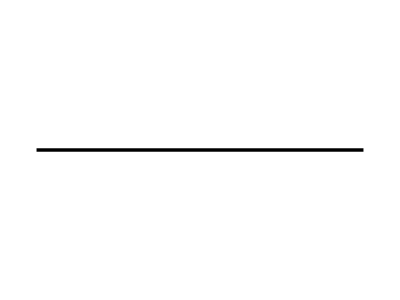
```mathematica
vizColors=RGBColor/@{"#2a78d6","#eb6834","#1baf7a","#eda100","#e87ba4"};vizMuted=RGBColor["#898781"];vizStyle[title_String,xlabel_,ylabel_]:={Frame->True,Axes->False,Background->RGBColor["#fcfcfb"],ImageSize->760,AspectRatio->0.58,FrameStyle->Directive[RGBColor["#c3c2b7"],AbsoluteThickness[1]],FrameTicksStyle->Directive[RGBColor["#52514e"],FontFamily->"Arial",FontSize->12],GridLines->Automatic,GridLinesStyle->Directive[RGBColor["#e1e0d9"],AbsoluteThickness[0.6]],FrameLabel->{Style[xlabel,RGBColor["#52514e"],FontFamily->"Arial",13],Style[ylabel,RGBColor["#52514e"],FontFamily->"Arial",13]},PlotLabel->Style[title,RGBColor["#0b0b0b"],FontFamily->"Arial",14],LabelStyle->Directive[RGBColor["#0b0b0b"],FontFamily->"Arial",FontSize->12],ImagePadding->{{70,20},{55,35}}};dotLineLegend[labels_List,colors_List,kinds_List]:=Placed[SwatchLegend[colors,labels,LegendMarkers->(If[#1==="dot",-Graphics-,-Graphics-]&)/@kinds,LegendMarkerSize->16,LabelStyle->Directive[RGBColor["#0b0b0b"],FontFamily->"Arial",FontSize->12],LegendLayout->{"Row",2}],Below];exportFigure[name_String,graphic_]:=Module[{path=FileNameJoin[{figureDirectory,name}],bytes,out,i=9,n,type,stream},Quiet[Export[path,graphic,"PNG",ImageResolution->110],{ImportExport`RegisterFormat::interr}];bytes=Normal[ReadByteArray[path]];out=Take[bytes,8];While[i≤Length[bytes],n=FromDigits[bytes⟦i;;i+3⟧,256];type=FromCharacterCode[bytes⟦i+4;;i+7⟧];If[!(type==="tEXt"&&StringStartsQ[FromCharacterCode[bytes⟦i+8;;i+7+n⟧],"Creation Time"]),out=Join[out,bytes⟦i;;i+11+n⟧]];i+=12+n];stream=OpenWrite[path,BinaryFormat->True];BinaryWrite[stream,out];Close[stream];name];figureFiles={};numberLabel[x_]:=If[x==Round[x],ToString[Round[x]],ToString[x]];sciLabel[x_]:=If[x==0,"0",Module[{e=Floor[Log10[Abs[x]]],mant},mant=Round[(100 Abs[x])/10^e];If[mant==1000,mant=100;e=e+1];If[x<0,"-",""]<>ToString[Quotient[mant,100]]<>"."<>IntegerString[Mod[mant,100],10,2]<>"e"<>ToString[e]]];{Length[vizColors],DirectoryQ[figureDirectory]}
```

```mathematica
Module[{res=exp1RunResults["A1_K2_mix"],ts,rhoR,p0R,ndObs,g},ts=res["t"];rhoR=Transpose[{ts,res["observables"]⟦All,"rho"⟧}];p0R=Transpose[{ts,res["observables"]⟦All,"p_0"⟧}];ndObs=(observables1[SelectFirst[summaries["exp1"]["runs"],#1["id"]==="A1_K2_mix"&],complexSpinor[#1]]&)/@res["ndsolve"];g=Legended[Show[ListLinePlot[{Transpose[{ts,ndObs⟦All,"rho"⟧}],Transpose[{ts,ndObs⟦All,"p_0"⟧}]},PlotStyle->(Directive[#1,AbsoluteThickness[2]]&)/@vizColors⟦1;;2⟧,PlotRange->All],ListPlot[{rhoR⟦1;;-1;;4⟧,p0R⟦1;;-1;;4⟧},PlotStyle->(Directive[#1,AbsolutePointSize[7]]&)/@vizColors⟦1;;2⟧],Sequence@@vizStyle["EXP-1 mixed state, K = 2: rho frozen, hidden-space pressure p_0 oscillates at 2E","t = H x4","density / pressure"]],dotLineLegend[{"rho, Rust CSV","rho, NDSolve","p_0, Rust CSV","p_0, NDSolve"},vizColors⟦{1,1,2,2}⟧,{"dot","line","dot","line"}]];AppendTo[figureFiles,exportFigure["exp1_mixed_state_rho_p0.png",g]];g]
```

```mathematica
Module[{curves,dots,g},curves=Table[Module[{amp=Rationalize[N[bg["amplitude"]]]},Table[{tt,-N[einstein1⟦5,5⟧/.{a4'[_]->a4PrimeProfile[amp,tt],a4''[_]->a4SecondProfile[amp,tt],hH->1}]},{tt,0.,10.,0.02}]],{bg,summaries["exp1"]["backgrounds"]}];dots=Table[Module[{run=readRun[FileNameJoin[{numericsRoot,"exp1",bg["file"]}]]},Transpose[{columnOf[run,"t"],columnOf[run,"rho_req"]}]⟦1;;-1;;4⟧],{bg,summaries["exp1"]["backgrounds"]}];g=Legended[Show[ListLinePlot[curves,PlotStyle->(Directive[#1,AbsoluteThickness[2]]&)/@vizColors⟦1;;2⟧,PlotRange->All],ListPlot[dots,PlotStyle->(Directive[#1,AbsolutePointSize[7]]&)/@vizColors⟦1;;2⟧],Sequence@@vizStyle["EXP-1 Einstein requirement rho_req = -G^4_4/kappa of the primordial field (always negative)","t = H x4","rho_req (kappa = H = 1)"]],dotLineLegend[{"A = 1, Rust CSV","A = 1, Mathematica G^4_4","A = 2, Rust CSV","A = 2, Mathematica G^4_4"},vizColors⟦{1,1,2,2}⟧,{"dot","line","dot","line"}]];AppendTo[figureFiles,exportFigure["exp1_einstein_requirement.png",g]];g]
```

```mathematica
Module[{res=exp2RunResults["x0_0"],lnV,lnVN,frac,fracN,g},lnV=res["state"]⟦All,1⟧+3 res["state"]⟦All,2⟧+3 res["state"]⟦All,3⟧;lnVN=res["ndsolve"]⟦All,1⟧+3 res["ndsolve"]⟦All,2⟧+3 res["ndsolve"]⟦All,3⟧;frac[st_]:=((#1⟦4;;6⟧)/(#1⟦4⟧+3 #1⟦5⟧+3 #1⟦6⟧)&)/@st;g=Legended[Show[ListLinePlot[Table[Transpose[{lnVN,frac[res["ndsolve"]]⟦All,i⟧}],{i,3}],PlotStyle->(Directive[#1,AbsoluteThickness[2]]&)/@vizColors⟦1;;3⟧,PlotRange->All],ListPlot[Table[Transpose[{lnV,frac[res["state"]]⟦All,i⟧}]⟦1;;-1;;6⟧,{i,3}],PlotStyle->(Directive[#1,AbsolutePointSize[7]]&)/@vizColors⟦1;;3⟧],Sequence@@vizStyle["EXP-2 dust (x0 = 0): H_i/Theta from the Kasner-type singularity to isotropic 8D dust (1/7)","ln V","H_i / Theta"]],dotLineLegend[{"H_b, Rust","H_b, NDSolve","H_a, Rust","H_a, NDSolve","H_c, Rust","H_c, NDSolve"},vizColors⟦{1,1,2,2,3,3}⟧,{"dot","line","dot","line","dot","line"}]];AppendTo[figureFiles,exportFigure["exp2_anisotropy_fractions.png",g]];g]
```

```mathematica
Module[{ids,lines,dots,cpl,g},ids=Select[Keys[exp3RunResults],StringEndsQ[#1,"_mu3"]&];lines=Table[Select[Transpose[{exp3RunResults[id]["a"],exp3RunResults[id]["wNDSolve"]}],-3≤#1⟦2⟧≤1&],{id,ids}];dots=Table[Select[Transpose[{exp3RunResults[id]["a"],exp3RunResults[id]["wRust"]}]⟦1;;-1;;8⟧,-3≤#1⟦2⟧≤1&],{id,ids}];cpl=Table[{av,-0.861-0.6 (1-av)},{av,0.3,2.,0.01}];g=Legended[Show[ListLinePlot[Append[lines,cpl],PlotStyle->Append[(Directive[#1,AbsoluteThickness[2]]&)/@vizColors⟦1;;Length[ids]⟧,Directive[vizMuted,AbsoluteThickness[1.5],Dashing[{0.02,0.012}]]],PlotRange->{{0.28,2.02},{-3,1}}],ListPlot[dots,PlotStyle->(Directive[#1,AbsolutePointSize[6]]&)/@vizColors⟦1;;Length[ids]⟧],Sequence@@vizStyle["EXP-3 w(a) of the condensate (dots: Rust CSV, lines: NDSolve; clipped to [-3, 1])","scale factor a","w = p_psi / rho_psi"]],Placed[SwatchLegend[Append[vizColors⟦1;;Length[ids]⟧,vizMuted],Append[("x0 = "<>If[exp3RunResults[#1]["x0"]==0,"0 (dust)",numberLabel[exp3RunResults[#1]["x0"]]]&)/@ids,"Unite CPL (-0.861, -0.60), reference"],LegendMarkers->-Graphics-,LegendMarkerSize->16,LabelStyle->Directive[RGBColor["#0b0b0b"],FontFamily->"Arial",FontSize->12],LegendLayout->{"Row",3}],Below]];AppendTo[figureFiles,exportFigure["exp3_equation_of_state.png",g]];g]
```

```mathematica
Module[{wR,wK,g},wR=Transpose[{Log10[thermalA],columnOf[thermalEOS,"w"]}];wK=Transpose[{Log10[thermalA],kineticTable⟦All,2⟧/kineticTable⟦All,1⟧}];g=Legended[Show[ListLinePlot[{wK},PlotStyle->{Directive[vizColors⟦1⟧,AbsoluteThickness[2]]},PlotRange->{{-0.02,2.02},{0,0.35}}],ListPlot[{wR⟦1;;-1;;2⟧},PlotStyle->{Directive[vizColors⟦2⟧,AbsolutePointSize[7]]}],Sequence@@vizStyle["EXP-4 thermal dirac16complex gas: w from radiation (1/3) towards dust (0)","log10 a","w = p / rho"]],dotLineLegend[{"Rust CVODE mode sum (48 modes)","Mathematica NIntegrate kinetic theory"},vizColors⟦{2,1}⟧,{"dot","line"}]];AppendTo[figureFiles,exportFigure["exp4_thermal_equation_of_state.png",g]];g]
```

```mathematica
Module[{masses={0.5,1.,2.},lines,dots,g},lines=Table[Module[{rows=Select[pairSpectrum["rows"],#1⟦pairSpectrum["index"]["m"]⟧==mass&&#1⟦pairSpectrum["index"]["beta2_end"]⟧>0&]},Transpose[{Log10[rows⟦All,pairSpectrum["index"]["k"]⟧],Log10[rows⟦All,pairSpectrum["index"]["beta2_end"]⟧]}]],{mass,masses}];dots=Table[Table[{Log10[pairResults[{mass,node}]["k"]],Log10[pairResults[{mass,node}]["beta2EndNDSolve"]]},{node,{16,32,48}}],{mass,masses}];g=Legended[Show[ListLinePlot[lines,PlotStyle->(Directive[#1,AbsoluteThickness[2]]&)/@vizColors⟦1;;3⟧,PlotRange->All],ListPlot[dots,PlotStyle->(Directive[#1,AbsolutePointSize[9]]&)/@vizColors⟦1;;3⟧],Sequence@@vizStyle["EXP-4 pair creation, de Sitter -> radiation: |beta_k|^2 at the end (lines: Rust spectrum, dots: NDSolve subset)","log10 k","log10 |beta_k|^2"]],dotLineLegend[Flatten[Table[{"m/H_inf = "<>numberLabel[mass]<>", Rust","m/H_inf = "<>numberLabel[mass]<>", NDSolve"},{mass,masses}]],vizColors⟦{1,1,2,2,3,3}⟧,{"line","dot","line","dot","line","dot"}]];AppendTo[figureFiles,exportFigure["exp4_pair_spectrum.png",g]];g]
```

```mathematica
Module[{ids={"q0p05_Cp","q0p1_Cp"},lines,dots,wkb,g},lines=Table[Transpose[{exp5RunResults[id]["t"],exp5RunResults[id]["lnNormNDSolve"]}],{id,ids}];dots=Table[Transpose[{exp5RunResults[id]["t"],exp5RunResults[id]["lnNormRust"]}]⟦1;;-1;;12⟧,{id,ids}];wkb=Table[Module[{q=exp5RunResults[id]["q"],ts=exp5RunResults[id]["t"],lnR=exp5RunResults[id]["lnNormRust"],iA},iA=Length[ts]-150;Table[{ts⟦j⟧,lnR⟦iA⟧+2 (wkbW[q,ts⟦j⟧]-wkbW[q,ts⟦iA⟧])},{j,iA,Length[ts],10}]],{id,ids}];g=Legended[Show[ListLinePlot[Join[lines,wkb],PlotStyle->Join[(Directive[#1,AbsoluteThickness[2]]&)/@vizColors⟦1;;2⟧,(Directive[#1,AbsoluteThickness[1.5],Dashing[{0.015,0.012}]]&)/@{vizMuted,vizMuted}],PlotRange->All],ListPlot[dots,PlotStyle->(Directive[#1,AbsolutePointSize[7]]&)/@vizColors⟦1;;2⟧],Sequence@@vizStyle["EXP-5 extra-time momentum q: ln(u^dagger u) grows as 2 W(t) after t* = ln(m/q)","t = H x4","ln(u^dagger u)"]],dotLineLegend[{"q = 0.05, Rust","q = 0.05, NDSolve","q = 0.1, Rust","q = 0.1, NDSolve","leading WKB 2 Delta W"},Join[vizColors⟦{1,1,2,2}⟧,{vizMuted}],{"dot","line","dot","line","line"}]];AppendTo[figureFiles,exportFigure["exp5_hilbert_norm_growth.png",g]];g]
```

```mathematica
Module[{labels,values,g},labels={"EXP-1 state","EXP-2 ln h_i","EXP-2 H_i/Theta","EXP-2 spinor (aligned)","EXP-3 spinor","EXP-3 ln sigma","EXP-4 thermal (aligned)","EXP-4 pair (aligned)","EXP-5 state (relative)"};values={exp1Result["ndsolve"]["maxAbsStateDeviationVsRust"],exp2Result["ndsolve"]["lnScaleMaxAbsDeviation"],exp2Result["ndsolve"]["hubbleMaxDeviationOverTheta"],exp2Result["ndsolve"]["spinorMaxPhaseAlignedDeviation"],exp3Result["ndsolve"]["spinorMaxAbsDeviation"],exp3Result["ndsolve"]["lnSigmaMaxAbsDeviation"],exp4Result["thermal"]["maxPhaseAlignedDeviation"],exp4Result["pair"]["maxPhaseAlignedDeviation"],exp5Result["ndsolve"]["maxRelativeStateDeviation"]};g=BarChart[-Log10[values],ChartStyle->vizColors⟦1⟧,BarOrigin->Left,BarSpacing->0.35,ChartLabels->Placed[(Style[#1,RGBColor["#52514e"],FontFamily->"Arial",12]&)/@labels,Before],LabelingFunction->(Placed[Style["max dev "<>sciLabel[10^-#1],RGBColor["#0b0b0b"],FontFamily->"Arial",11],After]&),Frame->{{False,False},{True,False}},FrameStyle->Directive[RGBColor["#c3c2b7"],AbsoluteThickness[1]],FrameTicksStyle->Directive[RGBColor["#52514e"],FontFamily->"Arial",FontSize->12],FrameLabel->{{None,None},{Style["digits of agreement, -log10(max deviation)",RGBColor["#52514e"],FontFamily->"Arial",13],None}},PlotLabel->Style["Agreement of NDSolve with the Rust CVODE solution",RGBColor["#0b0b0b"],FontFamily->"Arial",14],GridLines->{Automatic,None},GridLinesStyle->Directive[RGBColor["#e1e0d9"],AbsoluteThickness[0.6]],Background->RGBColor["#fcfcfb"],ImageSize->760,AspectRatio->0.62,ImagePadding->{{200,30},{55,35}},PlotRange->{{0,18},All}];AppendTo[figureFiles,exportFigure["cross_check_deviations.png",g]];g]
```

## Report and fail-fast verification

Summary of the measured deviations (all computed above; NDSolve = the independent Mathematica integration, Rust = the committed CVODE CSV output). Deviations are absolute unless marked relative.

```mathematica
findingsRows={{"EXP-1","state, NDSolve vs Rust",exp1Result["ndsolve"]["maxAbsStateDeviationVsRust"]},{"EXP-1","state, Rust vs exact propagator",exp1Result["ndsolve"]["maxExactErrorRust"]},{"EXP-1","state, NDSolve vs exact propagator",exp1Result["ndsolve"]["maxExactErrorNDSolve"]},{"EXP-1","RHS, 9-point FD residual (relative)",exp1Result["finiteDifference"]["maxRelativeResidual"]},{"EXP-2","ln h_i, NDSolve vs Rust",exp2Result["ndsolve"]["lnScaleMaxAbsDeviation"]},{"EXP-2","ln h_i, Rust vs closed form",exp2Result["ndsolve"]["rustLnScaleVsExact"]},{"EXP-2","ln h_i, NDSolve vs closed form",exp2Result["ndsolve"]["ndsolveLnScaleVsExact"]},{"EXP-2","H_i/Theta, NDSolve vs Rust",exp2Result["ndsolve"]["hubbleMaxDeviationOverTheta"]},{"EXP-2","spinor raw / phase-aligned, NDSolve vs Rust",{exp2Result["ndsolve"]["spinorMaxAbsDeviation"],exp2Result["ndsolve"]["spinorMaxPhaseAlignedDeviation"]}},{"EXP-2","Rust-reported spinor phase error (summary.json)",exp2Result["ndsolve"]["rustReportedMaxSpinorPhaseError"]},{"EXP-2","spinor vs exact solution, Rust / NDSolve",{exp2Result["ndsolve"]["rustSpinorVsExact"],exp2Result["ndsolve"]["ndsolveSpinorVsExact"]}},{"EXP-2","RHS FD residual, gravity / spinor (relative)",{exp2Result["finiteDifference"]["gravityMaxRelativeResidual"],exp2Result["finiteDifference"]["spinorMaxRelativeResidual"]}},{"EXP-3","H0 t, D_C (relative), NDSolve vs Rust",exp3Result["ndsolve"]["clockMaxRelativeDeviation"]},{"EXP-3","spinor, NDSolve vs Rust",exp3Result["ndsolve"]["spinorMaxAbsDeviation"]},{"EXP-3","ln sigma, NDSolve vs Rust",exp3Result["ndsolve"]["lnSigmaMaxAbsDeviation"]},{"EXP-3","spinor vs exact solution, Rust / NDSolve",{exp3Result["ndsolve"]["rustSpinorVsExact"],exp3Result["ndsolve"]["ndsolveSpinorVsExact"]}},{"EXP-3","RHS FD residual (relative)",exp3Result["finiteDifference"]["maxRelativeResidual"]},{"EXP-4","thermal spinor raw / phase-aligned",{exp4Result["thermal"]["maxAbsDeviation"],exp4Result["thermal"]["maxPhaseAlignedDeviation"]}},{"EXP-4","thermal bilinears eps/E, p_1/E, s, beta^2, norm",exp4Result["thermal"]["maxInvariantDeviation"]},{"EXP-4","thermal one-interval propagation",exp4Result["thermal"]["oneIntervalMaxAbsDeviation"]},{"EXP-4","thermal node 2, NDSolve Adams vs order-8 Runge-Kutta",exp4Result["thermal"]["ndsolveAdamsVsRungeKuttaNode2"]},{"EXP-4","rho / p mode sums vs NIntegrate (relative)",{thermalKinetic["rhoModeSumMaxRelativeDeviation"],thermalKinetic["pModeSumMaxRelativeDeviation"]}},{"EXP-4","pair spinor phase-aligned / |beta|^2 (relative)",{exp4Result["pair"]["maxPhaseAlignedDeviation"],exp4Result["pair"]["maxBeta2RelativeDeviation"]}},{"EXP-4","massless |beta|^2 at the end (NDSolve)",exp4Result["pair"]["masslessBeta2EndNDSolve"]},{"EXP-5","state (relative), NDSolve vs Rust",exp5Result["ndsolve"]["maxRelativeStateDeviation"]},{"EXP-5","NDSolve vs WorkingPrecision 32 (relative)",exp5Result["ndsolve"]["ndsolveSelfRelativeError"]},{"EXP-5","Krein drift / max(u^dagger u, 1), NDSolve",exp5Result["ndsolve"]["maxKreinDriftNormalised"]},{"EXP-5","growth vs WKB leading / first order (relative, max)",{Max[Abs[(#1["relDevRustVsWkbLeading"]&)/@Values[exp5RunResults]]],Max[Abs[(#1["relDevRustVsWkbFirstOrder"]&)/@Values[exp5RunResults]]]}}};Grid[Prepend[({#1⟦1⟧,#1⟦2⟧,StringRiffle[sciLabel/@Flatten[{#1⟦3⟧}]," / "]}&)/@findingsRows,{"experiment","quantity","value"}],Frame->All,Alignment->Left]
```

All checks are collected in notebookChecks; the report artifacts/dirac16complex/numerics/mathematica-report.json records every deviation above (numbers only, no timings, so repeated runs on the same machine give the same file).

The run parameters quoted in the text cells of this notebook are checked against the committed summary.json files, so that the prose cannot drift from the outputs.

```mathematica
textParameterChecks=Module[{p1=summaries["exp1"]["parameters"],p2=summaries["exp2"]["parameters"],p3=summaries["exp3"]["parameters"],p4=summaries["exp4"]["parameters"],p5=summaries["exp5"]["parameters"]},Association["exp1"->N[{p1["windowT1"],p1["windowT2"],p1["windowWidth"]}]=={2.,7.,0.5}&&N[p1["amplitudes"]]=={1.,2.}&&N[p1["hiddenMomenta"]]=={0.,0.5,2.}&&N[p1["lambdaCoupling"]]==0.5&&N[{p1["H"],p1["m"],p1["kappa"]}]=={1.,1.,1.},"exp2"->N[p2["x0Values"]]=={0.,-0.4,0.5}&&N[{p2["hubbleB0"],p2["hubbleA0"],p2["hubbleC0"],p2["kappa"]}]=={0.,1.,-0.2,1.},"exp3"->N[p3["x0Values"]]=={-0.462654,-0.433107,-0.3,-0.2,0.}&&N[p3["muValues"]]=={3.,7.},"exp4"->N[Lookup[p4["thermal"],{"m","temperature","hubbleInitial","tInitial","aEnd"}]]=={1.,10.,0.05,10.,100.}&&N[Lookup[p4["pair"],{"hubbleInflation","kOverAStart"}]]=={1.,200.}&&SubsetQ[N[p4["pair"]["masses"]],{0.,0.5,1.,2.}],"exp5"->N[{p5["H"],p5["m"],p5["extraTime"],p5["wkbWindowStart"]}]=={1.,1.,3.,1.5}]];textParameterChecks
```

```mathematica
notebookChecks=Join[KeyMap["algebra_"<>#1&,algebraIdentities],KeyMap["rustConstants_"<>#1&,rustConstantChecks],exp1Checks,exp2Checks,exp3Checks,exp4Checks,exp5Checks,KeyMap["engine_"<>#1&,engineChecks],Association["textParametersMatchSummaries"->And@@Values[textParameterChecks],"figuresExported"->Length[figureFiles]==8&&AllTrue[figureFiles,FileExistsQ[FileNameJoin[{figureDirectory,#1}]]&]]];jsonReady[a_Association]:=jsonReady/@a;jsonReady[l_List]:=jsonReady/@l;jsonReady[x_Real]:=If[Abs[x]<1/10^300,0.,x];jsonReady[x_Rational]:=N[x];jsonReady[_Missing]:=Null;jsonReady[x_]:=x;mathematicaReport=jsonReady[Association["schemaVersion"->1,"generatedBy"->"notebooks/Dirac16ComplexDarkSector.nb (built by scripts/build_dirac16complex_mathematica_notebook.wls, evaluated headless by scripts/verify_dirac16complex_mathematica_notebook.wls)","provenance"->"New notebook: none of the three rustSolveIt repositories (Win11 a8fdff45, macOS 5360157f, Linux 6f58e02e) contains a Mathematica notebook (verified by listing their full git trees; each has 294 Jupyter notebooks). Modelled on dirac-main notebooks/DiracTriality.nb and scripts/build_mathematica_notebook.wls / verify_mathematica_notebook.wls.","wolframVersion"->$VersionNumber,"fixtureSha256"->fixtureHash,"inputs"->"artifacts/dirac16complex/numerics/exp1..exp5 (CSV + summary.json), studies/dirac16complex_cosmology/src/generated.rs, artifacts/dirac16complex/arbitrary-field/algebra-fixture.json","method"->Association["symbolic"->"reduced mode equations from gamma^mu D_mu Psi = M_eff Psi (Dirac16ComplexGeometry symbolic geometry) and Einstein tensors, compared exactly with the Rust mode Hamiltonian and RHS","finiteDifference"->"9-point finite-difference derivatives of the CSV solutions vs the derived RHS; truncation estimate |D6 - D8|; rows with (|f|/|y|)(t_(n+4) - t_(n-4)) > 4 are under-resolved by the output grid and are excluded and counted","ndsolve"->"independent re-integration from the CSV initial states; deviations are max over all samples and components (relative where stated)"],"algebra"->algebraIdentities,"rustConstants"->rustConstantChecks,"textParameters"->textParameterChecks,"exp1"->exp1Result,"exp2"->exp2Result,"exp3"->exp3Result,"exp4"->exp4Result,"exp5"->exp5Result,"engine"->Association["binary"->"studies/dirac16complex_cosmology/target/release/"<>FileNameTake[binaryPath],"command"->"print-config","exitCode"->printConfig["ExitCode"],"lastLine"->If[printConfigLines==={},"",Last[printConfigLines]],"checks"->engineChecks],"figures"->("artifacts/dirac16complex/numerics/figures/mathematica/"<>#1&)/@figureFiles,"checks"->notebookChecks,"checkCount"->Length[notebookChecks],"verdict"->If[And@@Values[notebookChecks],"SUCCESS","FAILURE"]]];reportText=StringReplace[ExportString[mathematicaReport,"RawJSON","Compact"->False],{"\r\n"->"\n","\\/"->"/"}]<>"\n";reportStream=OpenWrite[reportPath,BinaryFormat->True];BinaryWrite[reportStream,ToCharacterCode[reportText,"UTF-8"]];Close[reportStream];{Length[notebookChecks],mathematicaReport["verdict"],FileByteCount[reportPath]}
```

```mathematica
If[!And@@Values[notebookChecks],Failure["NotebookVerification",Association["FailedChecks"->Keys[Select[notebookChecks,!TrueQ[#1]&]]]],notebookChecks]
```